```mathematica
GE- NUMERICAL METHODS
```

```mathematica
PRACTICAL 1: BISECTION METHOD
```

```mathematica
Q1. Perform  14  iterations  to  find  a  root  of  x^3-17=0.
```

i | ai | bi | ci | f[ci]
0 | 2 | 3 | 2.5 | -1.375
1 | 2.5 | 3 | 2.75 | 3.796875
2 | 2.5 | 2.75 | 2.625 | 1.0878906
3 | 2.5 | 2.625 | 2.5625 | -0.17358398
4 | 2.5625 | 2.625 | 2.59375 | 0.44955444
5 | 2.5625 | 2.59375 | 2.578125 | 0.13609695
6 | 2.5625 | 2.578125 | 2.5703125 | -0.019214153
7 | 2.5703125 | 2.578125 | 2.5742188 | 0.058323562
8 | 2.5703125 | 2.5742188 | 2.5722656 | 0.019525267
9 | 2.5703125 | 2.5722656 | 2.5712891 | 0.00014820043
10 | 2.5703125 | 2.5712891 | 2.5708008 | -0.0095348152

Root after 11 iterations is 2.5708008

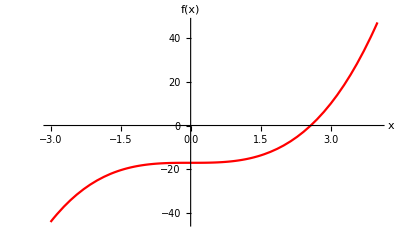

```mathematica
f[x_]:=x^3-17
a=2;b=3;c=N[(a+b)/2];
i=0;
If[f[a]*f[b]>0,
Print["We cannot find the roots in the given interval"],
OutputDetails={{i,a,b,c,f[c]}};
While[i<10,
If[f[a]*f[c]<0,b=c,a=c];
c=N[(a+b)/2];
i++;
OutputDetails=Append[OutputDetails,{i,a,b,c,f[c]}];];
Print[NumberForm[TableForm[OutputDetails,TableHeadings->{None,{"i","ai","bi","ci","f[ci]"}}],8]];
Print["Root after ",11," iterations is ",NumberForm[c,8]];
Plot[f[x],{x,-3,4},PlotStyle->{Red},AxesLabel->{"x","f(x)"}]]
```

```mathematica
Q2. Perform  15  iterations  to  find  a  root  of  Cos(x)=x.
```

i | ai | bi | ci | f[ci]
0 | 0 | 1 | 0.5 | 0.377583
1 | 0.5 | 1 | 0.75 | -0.0183111
2 | 0.5 | 0.75 | 0.625 | 0.185963
3 | 0.625 | 0.75 | 0.6875 | 0.0853349
4 | 0.6875 | 0.75 | 0.71875 | 0.0338794
5 | 0.71875 | 0.75 | 0.734375 | 0.00787473
6 | 0.734375 | 0.75 | 0.742188 | -0.00519571
7 | 0.734375 | 0.742188 | 0.738281 | 0.00134515
8 | 0.738281 | 0.742188 | 0.740234 | -0.00192387
9 | 0.738281 | 0.740234 | 0.739258 | -0.000289009
10 | 0.738281 | 0.739258 | 0.73877 | 0.000528158
11 | 0.73877 | 0.739258 | 0.739014 | 0.000119597
12 | 0.739014 | 0.739258 | 0.739136 | -0.0000847007
13 | 0.739014 | 0.739136 | 0.739075 | 0.0000174493
14 | 0.739075 | 0.739136 | 0.739105 | -0.0000336253

Root after 15 iterations is 0.739105

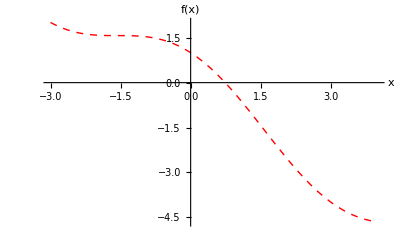

```mathematica
f[x_]:=Cos[x]-x
a=0;b=1;c=N[(a+b)/2];
i=0;
If[f[a]*f[b]>0,
Print["We cannot find the roots in the given interval"],
OutputDetails={{i,a,b,c,f[c]}};
While[i<14,
If[f[a]*f[c]<0,b=c,a=c];
c=N[(a+b)/2];
i++;
OutputDetails=Append[OutputDetails,{i,a,b,c,f[c]}];];
Print[NumberForm[TableForm[OutputDetails,TableHeadings->{None,{"i","ai","bi","ci","f[ci]"}}],6]];
Print["Root after ",15," iterations is ",NumberForm[c,6]];
Plot[f[x],{x,-3,4},PlotStyle->{Red,Dashed,Thick},AxesLabel->{"x","f(x)"}]]
```

```mathematica
Q3. Find the  root  of  the  function  f(x)=Cos(x)-x  by  bisection  method  such  that  f(xn)>0.0001.
```

```mathematica
f[x_]:=Cos[x]-x
a=0;b=1;c=N[(a+b)/2];
i=0;
If[f[a]*f[b]>0,
Print["We cannot find the roots in the given interval"],
OutputDetails={{i,a,b,c,f[c]}};
While[Abs[f[c]]>0.0001,
If[f[a]*f[c]<0,b=c,a=c];
c=N[(a+b)/2];
i++;
OutputDetails=Append[OutputDetails,{i,a,b,c,f[c]}];];
Print[NumberForm[TableForm[OutputDetails,TableHeadings->{None,{"i","ai","bi","ci","f[ci]"}}],6]];
Print["Root after ",15," iterations is ",NumberForm[c,6]];
Plot[f[x],{x,-3,4},PlotStyle->{Red,Dashed,Thick},AxesLabel->{"x","f(x)"}]]
```

i | ai | bi | ci | f[ci]
0 | 0 | 1 | 0.5 | 0.377583
1 | 0.5 | 1 | 0.75 | -0.0183111
2 | 0.5 | 0.75 | 0.625 | 0.185963
3 | 0.625 | 0.75 | 0.6875 | 0.0853349
4 | 0.6875 | 0.75 | 0.71875 | 0.0338794
5 | 0.71875 | 0.75 | 0.734375 | 0.00787473
6 | 0.734375 | 0.75 | 0.742188 | -0.00519571
7 | 0.734375 | 0.742188 | 0.738281 | 0.00134515
8 | 0.738281 | 0.742188 | 0.740234 | -0.00192387
9 | 0.738281 | 0.740234 | 0.739258 | -0.000289009
10 | 0.738281 | 0.739258 | 0.73877 | 0.000528158
11 | 0.73877 | 0.739258 | 0.739014 | 0.000119597
12 | 0.739014 | 0.739258 | 0.739136 | -0.0000847007

Root after 15 iterations is 0.739136

-Graphics-

```mathematica
Q4. Perform  15  iterations  to  find  a  root  of  Tan[Pi(x)] - x=0   over  the  interval  [0,1] .
```

i | ai | bi | ci | f[ci]
0 | 0 | 1 | 0.5 | 1.63312×10^16
1 | 0.5 | 1 | 0.75 | -1.75
2 | 0.5 | 0.75 | 0.625 | -3.03921
3 | 0.5 | 0.625 | 0.5625 | -5.58984
4 | 0.5 | 0.5625 | 0.53125 | -10.6844
5 | 0.5 | 0.53125 | 0.515625 | -20.8711
6 | 0.5 | 0.515625 | 0.507813 | -41.2433
7 | 0.5 | 0.507813 | 0.503906 | -81.9871
8 | 0.5 | 0.503906 | 0.501953 | -163.475
9 | 0.5 | 0.501953 | 0.500977 | -326.449
10 | 0.5 | 0.500977 | 0.500488 | -652.399
11 | 0.5 | 0.500488 | 0.500244 | -1304.3
12 | 0.5 | 0.500244 | 0.500122 | -2608.09
13 | 0.5 | 0.500122 | 0.500061 | -5215.69
14 | 0.5 | 0.500061 | 0.500031 | -10430.9

Root after 15 iterations is 0.500031

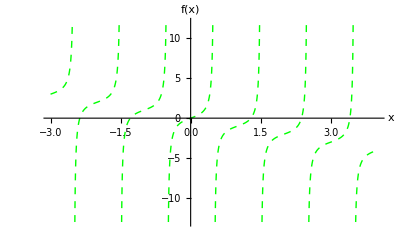

```mathematica
f[x_]:=Tan[Pi(x)]-x
a=0;b=1;c=N[(a+b)/2];
i=0;
If[f[a]*f[b]>0,
Print["We cannot find the roots in the given interval"],
OutputDetails={{i,a,b,c,f[c]}};
While[i<14,
If[f[a]*f[c]<0,b=c,a=c];
c=N[(a+b)/2];
i++;
OutputDetails=Append[OutputDetails,{i,a,b,c,f[c]}];];
Print[NumberForm[TableForm[OutputDetails,TableHeadings->{None,{"i","ai","bi","ci","f[ci]"}}],6]];
Print["Root after ",15," iterations is ",NumberForm[c,6]];
Plot[f[x],{x,-3,4},PlotStyle->{Green,Dashed,Thick},AxesLabel->{"x","f(x)"}]]
```

```mathematica
Q5. Perform 15 iterations to find  a root  of  Cos(x) - x*e^x=0 over  the  interval  [0,1] .
```

i | ai | bi | ci | f[ci]
0 | 0 | 1 | 0.5 | 0.0532219
1 | 0.5 | 1 | 0.75 | -0.856061
2 | 0.5 | 0.75 | 0.625 | -0.356691
3 | 0.5 | 0.625 | 0.5625 | -0.141294
4 | 0.5 | 0.5625 | 0.53125 | -0.0415122
5 | 0.5 | 0.53125 | 0.515625 | 0.00647534
6 | 0.515625 | 0.53125 | 0.523438 | -0.017362
7 | 0.515625 | 0.523438 | 0.519531 | -0.0054044
8 | 0.515625 | 0.519531 | 0.517578 | 0.000545184
9 | 0.517578 | 0.519531 | 0.518555 | -0.00242718
10 | 0.517578 | 0.518555 | 0.518066 | -0.000940389
11 | 0.517578 | 0.518066 | 0.517822 | -0.00019745
12 | 0.517578 | 0.517822 | 0.5177 | 0.000173905
13 | 0.5177 | 0.517822 | 0.517761 | -0.0000117633
14 | 0.5177 | 0.517761 | 0.517731 | 0.0000810732

Approximate root is 0.517731

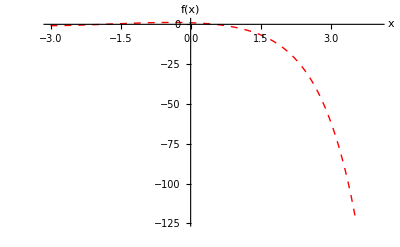

```mathematica
f[x_]:=Cos[x]-x*Exp[x]
a=0;b=1;c=N[(a+b)/2];
i=0;
If[f[a]*f[b]>0,
Print["We cannot find the roots in the given interval"],
OutputDetails={{i,a,b,c,f[c]}};
While[i<14,
If[f[a]*f[c]<0,b=c,a=c];
c=N[(a+b)/2];
i++;
OutputDetails=Append[OutputDetails,{i,a,b,c,f[c]}];];
Print[NumberForm[TableForm[OutputDetails,TableHeadings->{None,{"i","ai","bi","ci","f[ci]"}}],6]];
Print["Approximate root is ",NumberForm[c,6]];
Plot[f[x],{x,-3,4},PlotStyle->{Red,Dashed,Thick},AxesLabel->{"x","f(x)"}]]
```

```mathematica
Q6. Find the root of the  function f(x)=x^2+ 2x^2 - 3x-1  =0  by bisection method such that  f(xn)>0.00005.
```

i | ai | bi | ci | f[ci]
0 | 1 | 3 | 2. | 5.
1 | 1 | 2. | 1.5 | 1.25
2 | 1 | 1.5 | 1.25 | -0.0625
3 | 1.25 | 1.5 | 1.375 | 0.546875
4 | 1.25 | 1.375 | 1.3125 | 0.230469
5 | 1.25 | 1.3125 | 1.28125 | 0.0810547
6 | 1.25 | 1.28125 | 1.26563 | 0.00854492
7 | 1.25 | 1.26563 | 1.25781 | -0.0271606
8 | 1.25781 | 1.26563 | 1.26172 | -0.00935364
9 | 1.26172 | 1.26563 | 1.26367 | -0.000415802
10 | 1.26367 | 1.26563 | 1.26465 | 0.0040617
11 | 1.26367 | 1.26465 | 1.26416 | 0.00182223
12 | 1.26367 | 1.26416 | 1.26392 | 0.000703037
13 | 1.26367 | 1.26392 | 1.26379 | 0.000143573
14 | 1.26367 | 1.26379 | 1.26373 | -0.000136126
15 | 1.26373 | 1.26379 | 1.26376 | 3.72063×10^-6

Approximate root is 1.26376

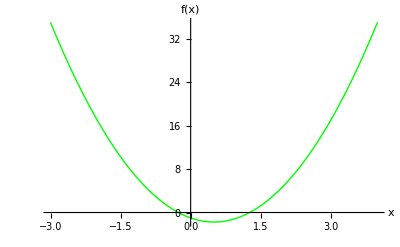

```mathematica
f[x_]:=x^2+2x^2-3x-1
a=1;b=3;c=N[(a+b)/2];
i=0;
If[f[a]*f[b]>0,
Print["We cannot find the roots in the given interval"],
OutputDetails={{i,a,b,c,f[c]}};
While[Abs[f[c]]>0.00005,
If[f[a]*f[c]<0,b=c,a=c];
c=N[(a+b)/2];
i++;
OutputDetails=Append[OutputDetails,{i,a,b,c,f[c]}];];
Print[NumberForm[TableForm[OutputDetails,TableHeadings->{None,{"i","ai","bi","ci","f[ci]"}}],6]];
Print["Approximate root is ",NumberForm[c,6]];
Plot[f[x],{x,-3,4},PlotStyle->{Green,Thick},AxesLabel->{"x","f(x)"}]]
```

```mathematica
Q7. Find  the  root  of  the  function  f(x)=x -(1 /37) =0  by  bisection  method  such  that  f(xn)>0.00005.
```

i | ai | bi | ci | f[ci]
0 | 0 | 1 | 0.5 | 0.472973
1 | 0 | 0.5 | 0.25 | 0.222973
2 | 0 | 0.25 | 0.125 | 0.097973
3 | 0 | 0.125 | 0.0625 | 0.035473
4 | 0 | 0.0625 | 0.03125 | 0.00422297
5 | 0 | 0.03125 | 0.015625 | -0.011402
6 | 0.015625 | 0.03125 | 0.0234375 | -0.00358953
7 | 0.0234375 | 0.03125 | 0.0273438 | 0.000316723
8 | 0.0234375 | 0.0273438 | 0.0253906 | -0.0016364
9 | 0.0253906 | 0.0273438 | 0.0263672 | -0.00065984
10 | 0.0263672 | 0.0273438 | 0.0268555 | -0.000171558
11 | 0.0268555 | 0.0273438 | 0.0270996 | 0.0000725823
12 | 0.0268555 | 0.0270996 | 0.0269775 | -0.000049488

Approximate root is 0.0269775

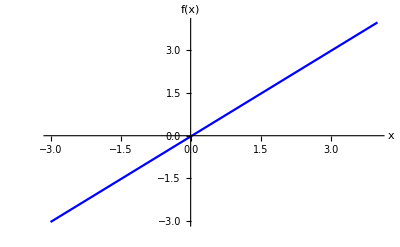

```mathematica
f[x_]:=x-(1/37)
a=0;b=1;c=N[(a+b)/2];
i=0;
If[f[a]*f[b]>0,
Print["We cannot find the roots in the given interval"],
OutputDetails={{i,a,b,c,f[c]}};
While[Abs[f[c]]>0.00005,
If[f[a]*f[c]<0,b=c,a=c];
c=N[(a+b)/2];
i++;
OutputDetails=Append[OutputDetails,{i,a,b,c,f[c]}];];
Print[NumberForm[TableForm[OutputDetails,TableHeadings->{None,{"i","ai","bi","ci","f[ci]"}}],6]];
Print["Approximate root is ",NumberForm[c,6]];
Plot[f[x],{x,-3,4},PlotStyle->{Blue},AxesLabel->{"x","f(x)"}]]
```

```mathematica
PRACTICAL 2(A): REGULA FALSI METHOD
```

```mathematica
Q1.  Perform  15  iterations  to  find  a  root  of  f(x)=tan(Pi[x])-x-6=0  using  false  position  method.
```

0

-6

0.48

9.41454

i | ai | bi | ci | f[ci]
0 | 0 | 0.48 | 0.186837 | -5.52167
1 | 0.186837 | 0.48 | 0.295214 | -4.96147
2 | 0.295214 | 0.48 | 0.358988 | -4.2513
3 | 0.358988 | 0.48 | 0.396633 | -3.42622
4 | 0.396633 | 0.48 | 0.418878 | -2.58038
5 | 0.418878 | 0.48 | 0.432026 | -1.82058
6 | 0.432026 | 0.48 | 0.4398 | -1.21543
7 | 0.4398 | 0.48 | 0.444397 | -0.778089
8 | 0.444397 | 0.48 | 0.447115 | -0.483741
9 | 0.447115 | 0.48 | 0.448722 | -0.295015
10 | 0.448722 | 0.48 | 0.449672 | -0.177747
11 | 0.449672 | 0.48 | 0.450234 | -0.106296
12 | 0.450234 | 0.48 | 0.450566 | -0.0632795
13 | 0.450566 | 0.48 | 0.450763 | -0.0375692
14 | 0.450763 | 0.48 | 0.450879 | -0.0222689
15 | 0.450879 | 0.48 | 0.450948 | -0.013187

Root after 15 iterations  is 0.450948

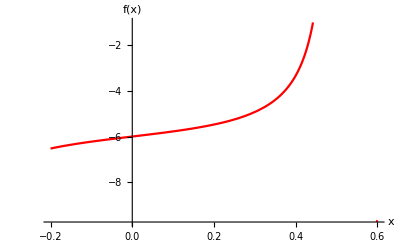

```mathematica
f[x_]:=Tan[Pi*x]-x-6;
a=0
f[a]
b=0.48
f[b]
c=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
i=0;
If[f[a]*f[b]>0,
Print["We cannot find the roots in the given interval" , "[",a,",",b,"]"],
OutputDetails={{i,a,b,c,f[c]}};
While[i<15,
If[f[a]*f[c]<0,b=c,a=c];
c=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
i++;
OutputDetails=Append[OutputDetails,{i,a,b,c,f[c]}];];
Print[NumberForm[TableForm[OutputDetails,
TableHeadings->{None,{"i","ai","bi","ci","f[ci]"}}],6]];
Print["Root after ",15 ," ", "iterations  is ",NumberForm[c,6]]];
Plot[f[x],{x,-0.2,0.6},PlotStyle->{Red},AxesLabel->{"x","f(x)"}]
```

```mathematica
Q2.  Find  a  root  of  the  function  f(x)=tan(Pi[x])-x-6=0  using  false  position  method  such  that  (f(x)_n)>0.0001.
```

i | ai | bi | ci | f[ci]
0 | 0 | 0.48 | 0.186837 | -5.52167
1 | 0.186837 | 0.48 | 0.295214 | -4.96147
2 | 0.295214 | 0.48 | 0.358988 | -4.2513
3 | 0.358988 | 0.48 | 0.396633 | -3.42622
4 | 0.396633 | 0.48 | 0.418878 | -2.58038
5 | 0.418878 | 0.48 | 0.432026 | -1.82058
6 | 0.432026 | 0.48 | 0.4398 | -1.21543
7 | 0.4398 | 0.48 | 0.444397 | -0.778089
8 | 0.444397 | 0.48 | 0.447115 | -0.483741
9 | 0.447115 | 0.48 | 0.448722 | -0.295015
10 | 0.448722 | 0.48 | 0.449672 | -0.177747
11 | 0.449672 | 0.48 | 0.450234 | -0.106296
12 | 0.450234 | 0.48 | 0.450566 | -0.0632795
13 | 0.450566 | 0.48 | 0.450763 | -0.0375692
14 | 0.450763 | 0.48 | 0.450879 | -0.0222689
15 | 0.450879 | 0.48 | 0.450948 | -0.013187
16 | 0.450948 | 0.48 | 0.450988 | -0.00780454
17 | 0.450988 | 0.48 | 0.451012 | -0.00461743
18 | 0.451012 | 0.48 | 0.451027 | -0.00273129
19 | 0.451027 | 0.48 | 0.451035 | -0.00161541
20 | 0.451035 | 0.48 | 0.45104 | -0.000955361
21 | 0.45104 | 0.48 | 0.451043 | -0.000564982
22 | 0.451043 | 0.48 | 0.451045 | -0.000334111
23 | 0.451045 | 0.48 | 0.451046 | -0.000197579
24 | 0.451046 | 0.48 | 0.451046 | -0.000116839
25 | 0.451046 | 0.48 | 0.451047 | -0.0000690925

approximate root is  0.451047

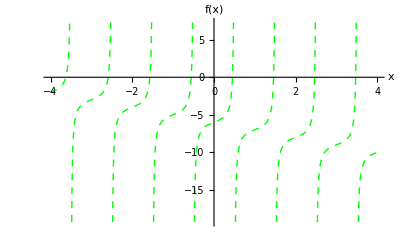

```mathematica
f[x_]:=Tan[Pi*x]-x-6
a=0;
b=0.48;
c=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
i=0;
If[f[a]*f[b]>0,
Print["We cannot find the roots in the given interval"],
OutputDetails={{i,a,b,c,f[c]}};
While[Abs[f[c]]>0.0001,
If[f[a]*f[c]<0,b=c,a=c];
c=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
i++;
OutputDetails=Append[OutputDetails,{i,a,b,c,f[c]}];];
Print[NumberForm[TableForm[OutputDetails,
TableHeadings->{None,{"i","ai","bi","ci","f[ci]"}}],6]];
Print["approximate root is "," ", NumberForm[c,6]]];
Plot[f[x],{x,-4,4},PlotStyle->{Green,Dashed,Thick},AxesLabel->{"x","f(x)"}]
```

#### Q3. Perform 10 iterations to find a root of q (X) = cos (x) - x*exp (x) using false position method.

i | ai | bi | ci | f[ci]
0 | 0 | 1 | 0.6127 | -0.0708139
1 | 0 | 0.6127 | 0.572181 | -0.00788827
2 | 0 | 0.572181 | 0.567703 | -0.000877392
3 | 0 | 0.567703 | 0.567206 | -0.0000975727
4 | 0 | 0.567206 | 0.56715 | -0.0000108506
5 | 0 | 0.56715 | 0.567144 | -1.20665×10^-6
6 | 0 | 0.567144 | 0.567143 | -1.34185×10^-7
7 | 0 | 0.567143 | 0.567143 | -1.49221×10^-8
8 | 0 | 0.567143 | 0.567143 | -1.65942×10^-9
9 | 0 | 0.567143 | 0.567143 | -1.84536×10^-10
10 | 0 | 0.567143 | 0.567143 | -2.05215×10^-11

Root after 10 iterations  is 0.567143

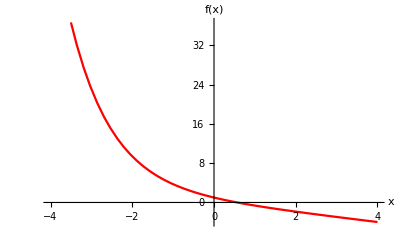

```mathematica
f[x_]:=Exp[-x]-x;
a=0;
b=1;
c=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
i=0;
If[f[a]*f[b]>0,
Print["We cannot find the roots in the given interval"],
OutputDetails={{i,a,b,c,f[c]}};
While[i<10,
If[f[a]*f[c]<0,b=c,a=c];
c=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
i++;
OutputDetails=Append[OutputDetails,{i,a,b,c,f[c]}];];
Print[NumberForm[TableForm[OutputDetails,
TableHeadings->{None,{"i","ai","bi","ci","f[ci]"}}],6]];
Print["Root after ",10 ," ", "iterations  is ",NumberForm[c,6]]];
Plot[f[x],{x,-4,4},PlotStyle->{Red},AxesLabel->{"x","f(x)"}]
```

#### Q4. Perform 15 iterations to find a root of f (x) = tan (pi*x) - x over the interval [0, 1].

i | ai | bi | ci | f[ci]
0 | 0 | 1 | 0. | 0.
1 | 0. | 1 | 0. | 0.
2 | 0. | 1 | 0. | 0.
3 | 0. | 1 | 0. | 0.
4 | 0. | 1 | 0. | 0.
5 | 0. | 1 | 0. | 0.
6 | 0. | 1 | 0. | 0.
7 | 0. | 1 | 0. | 0.
8 | 0. | 1 | 0. | 0.
9 | 0. | 1 | 0. | 0.
10 | 0. | 1 | 0. | 0.
11 | 0. | 1 | 0. | 0.
12 | 0. | 1 | 0. | 0.
13 | 0. | 1 | 0. | 0.
14 | 0. | 1 | 0. | 0.
15 | 0. | 1 | 0. | 0.

Root after 15 iterations  is 0.

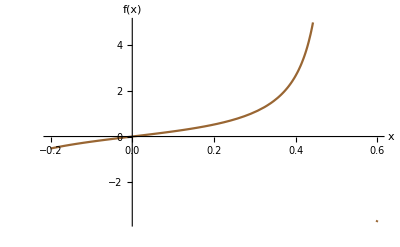

```mathematica
f[x_]:=Tan[Pi*x]-x;
a=0
b=1
c=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
i=0;
If[f[a]*f[b]>0,
Print["We cannot find the roots in the given interval" , "[",a,",",b,"]"],
OutputDetails={{i,a,b,c,f[c]}};
While[i<15,
If[f[a]*f[c]<0,b=c,a=c];
c=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
i++;
OutputDetails=Append[OutputDetails,{i,a,b,c,f[c]}];];
Print[NumberForm[TableForm[OutputDetails,
TableHeadings->{None,{"i","ai","bi","ci","f[ci]"}}],6]];
Print["Root after ",15 ," ", "iterations  is ",NumberForm[c,6]]];
Plot[f[x],{x,-0.2,0.6},PlotStyle->{Brown},AxesLabel->{"x","f(x)"}]
```

#### Q5. Perform 15 iterations to find a root of f(x)=Cos(x)-x*e^x =0 over the interval [0,1].

i | ai | bi | ci | f[ci]
0 | 0 | 1 | 0.314665 | 0.519871
1 | 0.314665 | 1 | 0.446728 | 0.203545
2 | 0.446728 | 1 | 0.494015 | 0.0708023
3 | 0.494015 | 1 | 0.509946 | 0.0236077
4 | 0.509946 | 1 | 0.515201 | 0.00776011
5 | 0.515201 | 1 | 0.516922 | 0.00253886
6 | 0.516922 | 1 | 0.517485 | 0.000829358
7 | 0.517485 | 1 | 0.517668 | 0.000270786
8 | 0.517668 | 1 | 0.517728 | 0.0000883971
9 | 0.517728 | 1 | 0.517748 | 0.0000288554
10 | 0.517748 | 1 | 0.517754 | 9.41909×10^-6
11 | 0.517754 | 1 | 0.517756 | 3.07459×10^-6
12 | 0.517756 | 1 | 0.517757 | 1.00361×10^-6
13 | 0.517757 | 1 | 0.517757 | 3.276×10^-7
14 | 0.517757 | 1 | 0.517757 | 1.06935×10^-7
15 | 0.517757 | 1 | 0.517757 | 3.4906×10^-8

Root after 16 iterations  is 0.517757

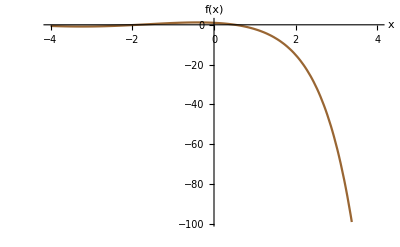

```mathematica
f[x_]:=Cos[x]-x*Exp[x];
a=0
b=1
c=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
i=0;
If[f[a]*f[b]>0,
Print["We cannot find the roots in the given interval" , "[",a,",",b,"]"],
OutputDetails={{i,a,b,c,f[c]}};
While[i<15,
If[f[a]*f[c]<0,b=c,a=c];
c=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
i++;
OutputDetails=Append[OutputDetails,{i,a,b,c,f[c]}];];
Print[NumberForm[TableForm[OutputDetails,
TableHeadings->{None,{"i","ai","bi","ci","f[ci]"}}],6]];
Print["Root after ",16 ," ", "iterations  is ",NumberForm[c,6]]];
Plot[f[x],{x,-4,4},PlotStyle->Brown,AxesLabel->{"x","f(x)"}]
```

#### Q6. Find a root of the function f(x)=x^3+2*x^2-3*x-1=0 using false position method such that f(x_n)<0.0005.

i | ai | bi | ci | f[ci]
0 | -1 | 0 | -0.25 | -0.140625
1 | -1 | -0.25 | -0.283582 | -0.0112215
2 | -1 | -0.283582 | -0.286252 | -0.000819699
3 | -1 | -0.286252 | -0.286447 | -0.0000594456

Approximate root is  -0.286447

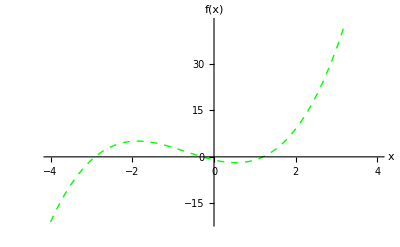

```mathematica
f[x_]:=x^3+2*x^2-3*x-1
a=-1;
b=0;
c=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
i=0;
If[f[a]*f[b]>0,
Print["We cannot find the roots in the given interval"],
OutputDetails={{i,a,b,c,f[c]}};
While[Abs[f[c]]>0.0005,
If[f[a]*f[c]<0,b=c,a=c];
c=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
i++;
OutputDetails=Append[OutputDetails,{i,a,b,c,f[c]}];];
Print[NumberForm[TableForm[OutputDetails,
TableHeadings->{None,{"i","ai","bi","ci","f[ci]"}}],6]];
Print["Approximate root is "," ", NumberForm[c,6]]];
Plot[f[x],{x,-4,4},PlotStyle->{Green,Dashed,Thick},AxesLabel->{"x","f(x)"}]
```

#### Q7. Find a root of the function f(X)=x-1/37=0 using false position method such that f(x_n)<0.0005.

i | ai | bi | ci | f[ci]
0 | 0 | 1 | 0.027027 | 0.

Approximate root is  0.027027

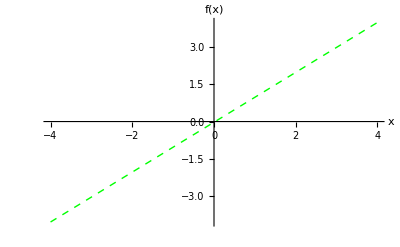

```mathematica
f[x_]:=x-1/37
a=0;
b=1;
c=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
i=0;
If[f[a]*f[b]>0,
Print["We cannot find the roots in the given interval"],
OutputDetails={{i,a,b,c,f[c]}};
While[Abs[f[c]]>0.0005,
If[f[a]*f[c]<0,b=c,a=c];
c=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
i++;
OutputDetails=Append[OutputDetails,{i,a,b,c,f[c]}];];
Print[NumberForm[TableForm[OutputDetails,
TableHeadings->{None,{"i","ai","bi","ci","f[ci]"}}],6]];
Print["Approximate root is "," ", NumberForm[c,6]]];
Plot[f[x],{x,-4,4},PlotStyle->{Green,Dashed,Thick},AxesLabel->{"x","f(x)"}]
```

```mathematica
PRACTICAL 2(B): SECANT METHOD
```

#### Q1. Find the root of f (x) = x^2 - 3 using secant method.

i | pi | f[pi]
0 | 1.66667 | -0.222222
1 | 1.72727 | -0.0165289
2 | 1.73214 | 0.000318878
3 | 1.73205 | -4.40416×10^-7
4 | 1.73205 | -1.17018×10^-11
5 | 1.73205 | 4.44089×10^-16
6 | 1.73205 | 4.44089×10^-16

Root after 6 iterations  is 1.73205

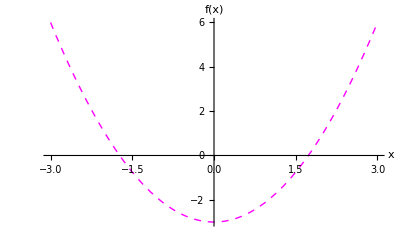

```mathematica
f[x_]:=x^2-3
a=1;
b=2;
p=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
i=0;
OutputDetails={{i,p,f[p]}};
While[i<6,
a=b;b=p;
i++;
p=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
OutputDetails=Append[OutputDetails,{i,p,f[p]}];];
Print[NumberForm[TableForm[OutputDetails,
TableHeadings->{None,{"i","pi","f[pi]"}}],6]];
Print["Root after ",6," ", "iterations  is ",NumberForm[p,6]];
Plot[f[x],{x,-3,3},PlotStyle->{Magenta,Dashed,Thick},AxesLabel->{"x","f(x)"}]
```

#### Q2. Find the root of f (x) = Tan (Pi*x) - x - 6 = 0 using secant method.

i | pi | f[pi]
0 | 0.420867 | -2.48159
1 | 0.433203 | -1.73804
2 | 0.462037 | 1.88285
3 | 0.447043 | -0.491858
4 | 0.450149 | -0.117251
5 | 0.451121 | 0.00977648
6 | 0.451046 | -0.000179101
7 | 0.451047 | -2.68665×10^-7
8 | 0.451047 | 7.39409×10^-12
9 | 0.451047 | 3.55271×10^-15
10 | 0.451047 | 3.55271×10^-15

Root after 10 iterations  is 0.451047

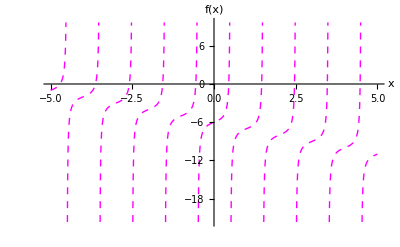

```mathematica
f[x_]:=Tan[Pi*x]-x-6
a=0.4;
b=0.48;
p=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
i=0;
OutputDetails={{i,p,f[p]}};
While[i<10,
a=b;b=p;
i++;
p=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
OutputDetails=Append[OutputDetails,{i,p,f[p]}];];
Print[NumberForm[TableForm[OutputDetails,
TableHeadings->{None,{"i","pi","f[pi]"}}],6]];
Print["Root after ",10," ", "iterations  is ",NumberForm[p,6]];
Plot[f[x],{x,-5,5},PlotStyle->{Magenta,Dashed,Thick},AxesLabel->{"x","f(x)"}]
```

#### Q3. Find the root of f(x)=tan(pi*x)-x-6 using secant method such that f(fx_n)>0.0001.

```mathematica
f[x_]:=Tan[Pi*x]-x-6
a=0.4;b=0.48;p=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
i=0;
OutputDetails={{i,p,f[p]}};
While[Abs[f[p]]>0.0001,
a=b;b=p;
i++;
p=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
OutputDetails=Append[OutputDetails,{i,p,f[p]}];];
Print[NumberForm[TableForm[OutputDetails,
TableHeadings->{None,{"i","pi","f[pi]"}}],6]];
Print["Approximate root is ",NumberForm[p,6]];
Plot[f[x],{x,-5,5},PlotStyle->{Magenta,Dashed,Thick},AxesLabel->{"x","f(x)"}]
```

i | pi | f[pi]
0 | 0.420867 | -2.48159
1 | 0.433203 | -1.73804
2 | 0.462037 | 1.88285
3 | 0.447043 | -0.491858
4 | 0.450149 | -0.117251
5 | 0.451121 | 0.00977648
6 | 0.451046 | -0.000179101
7 | 0.451047 | -2.68665×10^-7

Approximate root is 0.451047

-Graphics-

#### Q4. Find the root of f (x) = Tan (Pi*x) - x using secant method over the interval [1.2, 1.4].

i | pi | f[pi]
0 | 1.24401919 | -0.280908915
1 | 1.26639057 | -0.157713483
2 | 1.29503016 | 0.0371076327
3 | 1.28957517 | -0.00392970556
4 | 1.29009753 | -0.0000893178701
5 | 1.29010968 | 2.19719002×10^-7
6 | 1.29010965 | -1.22584165×10^-11
7 | 1.29010965 | 2.44249065×10^-15
8 | 1.29010965 | 4.4408921×10^-16
9 | 1.29010965 | -1.77635684×10^-15

Root after 9 iterations  is 1.29010965

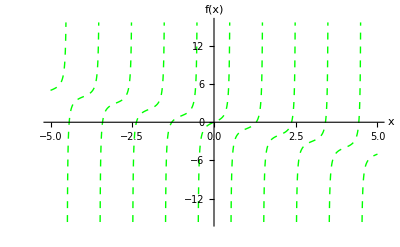

```mathematica
f[x_]:=Tan[Pi*x]-x
a=1.2;
b=1.4;
p=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
i=0;
OutputDetails={{i,p,f[p]}};
While[i<9,
a=b;b=p;
i++;
p=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
OutputDetails=Append[OutputDetails,{i,p,f[p]}];];
Print[NumberForm[TableForm[OutputDetails,
TableHeadings->{None,{"i","pi","f[pi]"}}],9]];
Print["Root after ",9," ", "iterations  is ",NumberForm[p,9]];
Plot[f[x],{x,-5,5},PlotStyle->{Green,Dashed,Thick},AxesLabel->{"x","f(x)"}]
```

#### Q5. Find the root of f(x)=Cos(x)-xe^x using secant method over the interval [0,1].

i | pi | f[pi]
0 | 0.314665338 | 0.519871174
1 | 0.446728145 | 0.203544778
2 | 0.531705861 | -0.0429310932
3 | 0.516904468 | 0.00259276314
4 | 0.517747465 | 0.0000301119411
5 | 0.517757371 | -2.15131646×10^-8
6 | 0.517757364 | 1.78079773×10^-13
7 | 0.517757364 | -3.33066907×10^-16
8 | 0.517757364 | 1.11022302×10^-16
9 | 0.517757364 | 1.11022302×10^-16

Root after 9 iterations  is 0.517757364

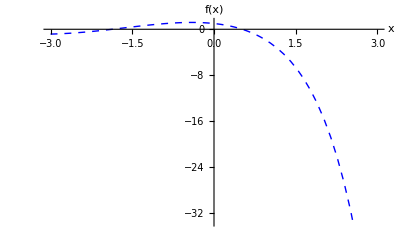

```mathematica
f[x_]:=Cos[x]-x*Exp[x]
a=0;
b=1;
p=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
i=0;
OutputDetails={{i,p,f[p]}};
While[i<9,
a=b;b=p;
i++;
p=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
OutputDetails=Append[OutputDetails,{i,p,f[p]}];];
Print[NumberForm[TableForm[OutputDetails,
TableHeadings->{None,{"i","pi","f[pi]"}}],9]];
Print["Root after ",9," ", "iterations  is ",NumberForm[p,9]];
Plot[f[x],{x,-3,3},PlotStyle->{Blue,Dashed,Thick},AxesLabel->{"x","f(x)"}]
```

#### Q6. Find the root of f(x)=x^3+2x^2-3*x-1=0 using secant method such that f(fx_n)>0.0005.

i | pi | f[pi]
0 | 0.5 | -1.875
1 | 1.57143 | 3.10496
2 | 0.903403 | -1.34063
3 | 1.10486 | -0.524449
4 | 1.2343 | 0.224557
5 | 1.19549 | -0.0194682
6 | 1.19859 | -0.000622339
7 | 1.19869 | 1.8289×10^-6

Approximate root is 1.19869

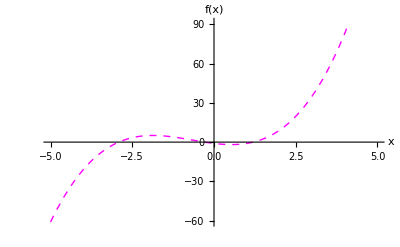

```mathematica
f[x_]:=x^3+2*x^2-3*x-1
a=-1;b=1;p=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
i=0;
OutputDetails={{i,p,f[p]}};
While[Abs[f[p]]>0.0005,
a=b;b=p;
i++;
p=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
OutputDetails=Append[OutputDetails,{i,p,f[p]}];];
Print[NumberForm[TableForm[OutputDetails,
TableHeadings->{None,{"i","pi","f[pi]"}}],6]];
Print["Approximate root is ",NumberForm[p,6]];
Plot[f[x],{x,-5,5},PlotStyle->{Magenta,Dashed,Thick},AxesLabel->{"x","f(x)"}]
```

#### Q7. Find the root of f(x)=x-1/37 using secant method such that f(fx_n)>0.0005.

i | pi | f[pi]
0 | 0.027027 | 0.

Approximate root is 0.027027

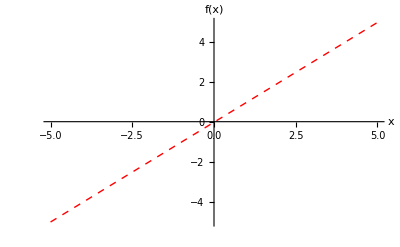

```mathematica
f[x_]:=x-1/37
a=0;b=1;p=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
i=0;
OutputDetails={{i,p,f[p]}};
While[Abs[f[p]]>0.0005,
a=b;b=p;
i++;
p=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
OutputDetails=Append[OutputDetails,{i,p,f[p]}];];
Print[NumberForm[TableForm[OutputDetails,
TableHeadings->{None,{"i","pi","f[pi]"}}],6]];
Print["Approximate root is ",NumberForm[p,6]];
Plot[f[x],{x,-5,5},PlotStyle->{Red,Dashed,Thick},AxesLabel->{"x","f(x)"}]
```

```mathematica
PRACTICAL 3: NEWTON RAPHSON METHOD
```

```mathematica
Q1. Find root of f(x)=log(1+x)-cos(x) using Newton method.
```

-Cos[x]+Log[1+x]

1/(1+x)+Sin[x]

{x→0.884511}

1.

i | pi | f[pi]
0 | 0 | -1
1 | 1. | 0.152845
2 | 0.886062 | 0.00202347
3 | 0.884511 | 4.22788×10^-7
4 | 0.884511 | 1.85407×10^-14
5 | 0.884511 | 0.
6 | 0.884511 | 0.
7 | 0.884511 | 0.
8 | 0.884511 | 0.
9 | 0.884511 | 0.
10 | 0.884511 | 0.
11 | 0.884511 | 0.
12 | 0.884511 | 0.
13 | 0.884511 | 0.

Root after 13 iterations is 0.884511

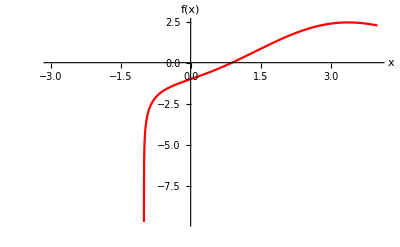

```mathematica
f[x_]=Log[1+x]-Cos[x]
g[x_]=D[f[x],x]
FindRoot[f[x],{x,4}]
p=0;
p1=N[p-(f[p]/g[p])]
i=0;
If[g[p]==0, Print["We cannot find the root in the given interval"];]
OutputDetails={{i,p,f[p]}};
While[i<13,i++;
p1=N[p-(f[p]/g[p])];
OutputDetails=Append[OutputDetails,{i,p1,f[p1]}];
p=p1];
Print[NumberForm[TableForm[OutputDetails,TableHeadings->{None,{"i","pi","f[pi]"}}],6]];
Print["Root after ", 13," iterations is ",NumberForm[p1,6]];
Plot[f[x], {x,-3,4},PlotStyle->{Red},AxesLabel->{"x","f(x)"}]
```

```mathematica
Q2. Find root of f (x)=x^2-2 using newton method.
```

2 x

{x→1.41421}

1.5

i | pi | f[pi]
0 | 1 | -1
1 | 1.5 | 0.25
2 | 1.41667 | 0.00694444
3 | 1.41422 | 6.0073×10^-6
4 | 1.41421 | 4.51061×10^-12
5 | 1.41421 | 4.44089×10^-16
6 | 1.41421 | -4.44089×10^-16
7 | 1.41421 | 4.44089×10^-16
8 | 1.41421 | -4.44089×10^-16
9 | 1.41421 | 4.44089×10^-16
10 | 1.41421 | -4.44089×10^-16
11 | 1.41421 | 4.44089×10^-16
12 | 1.41421 | -4.44089×10^-16
13 | 1.41421 | 4.44089×10^-16
14 | 1.41421 | -4.44089×10^-16
15 | 1.41421 | 4.44089×10^-16

Root after 15 iterations is 1.41421

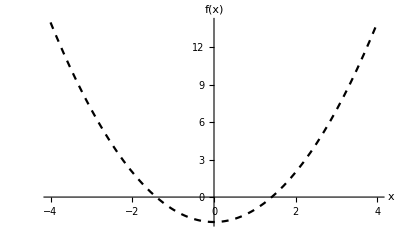

```mathematica
f[x_]=x^2-2;
g[x_]=D[f[x],x]
FindRoot[f[x],{x,1}]
p=1;
p1=N[p-(f[p]/g[p])]
i=0;
If[g[p]==0, Print["We cannot find the root in the given interval"];]
OutputDetails={{i,p,f[p]}};
While[i<15,i++;
p1=N[p-(f[p]/g[p])];
OutputDetails=Append[OutputDetails,{i,p1,f[p1]}];
p=p1];
Print[NumberForm[TableForm[OutputDetails,TableHeadings->{None,{"i","pi","f[pi]"}}],6]];
Print["Root after ", 15," iterations is ",NumberForm[p1,6]];
Plot[f[x], {x,-4,4},PlotStyle->{Black,Dashed},AxesLabel->{"x","f(x)"}]
```

#### Q3.Find the root of the function f(x)=x^2-2 by Newton Raphson method such that f(x_n)>0.0001.

-2+x^2

2 x

{x→1.41421}

i | pi | f[pi]
0 | 2 | 2
1 | 1.5 | 0.25
2 | 1.41667 | 0.00694444
3 | 1.41422 | 6.0073×10^-6

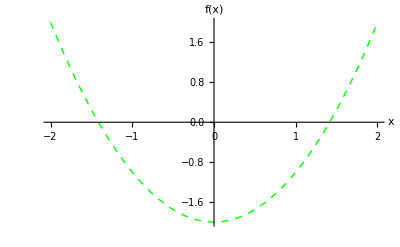

```mathematica
f[x_]=x^2-2
g[x_]=D[f[x],x]
FindRoot[f[x],{x,1}]
p=2;p1=N[p-f[p]/g[p]];
i=0;
If[g[p]==0,
Print["We cannot find the root in the given interval"];];
OutputDetails={{i,p,f[p]}};
While[Abs[f[p]]>0.0001,
i++;
p1=N[p-f[p]/g[p]];
OutputDetails=Append[OutputDetails,{i,p1,f[p1]}];
p=p1];
Print[NumberForm[TableForm[OutputDetails,TableHeadings->{None,{"i","pi","f[pi]"}}],6]];
Plot[f[x],{x,-2,+2},PlotStyle->{Green,Dashed,Thick},AxesLabel->{"x","f(x)"}]
```

```mathematica
Q4. Perform 10 iterations  to find the root of Tan(πx)-x=0 starting from Subscript[p, 0]=0
```

-1+π Sec[π x]^2

{x→1.29011}

i | pi | f[pi]
0 | 0 | 0
1 | 0. | 0.
2 | 0. | 0.
3 | 0. | 0.
4 | 0. | 0.
5 | 0. | 0.
6 | 0. | 0.
7 | 0. | 0.
8 | 0. | 0.
9 | 0. | 0.
10 | 0. | 0.

Root after 10 iterations is 0.

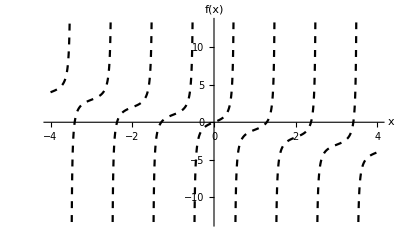

```mathematica
f[x_]=Tan[π*x]-x;
g[x_]=D[f[x],x]
FindRoot[f[x],{x,1}]
p=0;p1=N[p-f[p]/g[p]];
i=0;
If[g[p]==0,
Print["We cannot find the roots in the given interval"];];
OutputDetails={{i,p,f[p]}};
While[i<10,
i++;
p1=N[p-f[p]/g[p]];
OutputDetails=Append[OutputDetails,{i,p1,f[p1]}];
p=p1];
Print[NumberForm[TableForm[OutputDetails,TableHeadings->{None,{"i","pi","f[pi]"}}],6]];
Print["Root after ",10," iterations is ",NumberForm[p1,6]];
Plot[f[x],{x,-4,4},PlotStyle->{Black,Dashed},AxesLabel->{"x","f(x)"}]
```

```mathematica
Q5. Perform 10 iterations  to find the root of x^7-90=0.
```

7 x^6

{x→1.90186}

i | pi | f[pi]
0 | 1 | -89
1 | 13.7143 | 9.12456×10^7
2 | 11.7551 | 3.10159×10^7
3 | 10.0758 | 1.05428×10^7
4 | 8.63642 | 3.58365×10^6
5 | 7.40268 | 1.21812×10^6
6 | 6.34523 | 414035.
7 | 5.43896 | 140714.
8 | 4.66247 | 47807.2
9 | 3.99765 | 16226.8
10 | 3.42971 | 5492.14

Root after 10 iterations is 3.42971

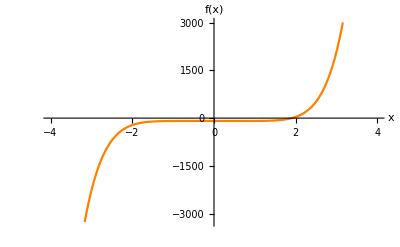

```mathematica
f[x_]=x^7-90;
g[x_]=D[f[x],x]
FindRoot[f[x],{x,1}]
p=1;p1=N[p-f[p]/g[p]];
i=0;
If[g[p]==0,
Print["We cannot find the roots in the given interval"];];
OutputDetails={{i,p,f[p]}};
While[i<10,
i++;
p1=N[p-f[p]/g[p]];
OutputDetails=Append[OutputDetails,{i,p1,f[p1]}];
p=p1];
Print[NumberForm[TableForm[OutputDetails,TableHeadings->{None,{"i","pi","f[pi]"}}],6]];
Print["Root after ",10," iterations is ",NumberForm[p1,6]];
Plot[f[x],{x,-4,4},PlotStyle->{Orange},AxesLabel->{"x","f(x)"}]
```

```mathematica
Q6. Perform Newton Raphson method to obtain approximate root Subscript[x, n] of  x^2-50.  Stop when f(Subscript[x, n])<0.0005.
```

-50+x^2

2 x

{x→7.07107}

i | pi | f[pi]
0 | 2 | -46

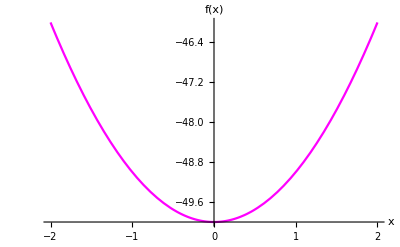

```mathematica
f[x_]=x^2-50
g[x_]=D[f[x],x]
FindRoot[f[x],{x,1}]
p=2;p1=N[p-f[p]/g[p]];
i=0;
If[g[p]==0,
Print["We cannot find the root in the given interval"];];
OutputDetails={{i,p,f[p]}};
While[Abs[f[p]]<0.0005,
i++;
p1=N[p-f[p]/g[p]];
OutputDetails=Append[OutputDetails,{i,p1,f[p1]}];
p=p1];
Print[NumberForm[TableForm[OutputDetails,TableHeadings->{None,{"i","pi","f[pi]"}}],6]];
Plot[f[x],{x,-2,+2},PlotStyle->{Magenta},AxesLabel->{"x","f(x)"}]
```

#### Q7.Perform Newton Raphson method to obtain approximate root x_n of Cos(x)-xe^x=0.Starting from p_0=0.5 . Stop when f(x_n)<0.0005

-ⅇ^x x+Cos[x]

-ⅇ^x-ⅇ^x x-Sin[x]

{x→0.517757}

i | pi | f[pi]
0 | 0.5 | 0.0532219

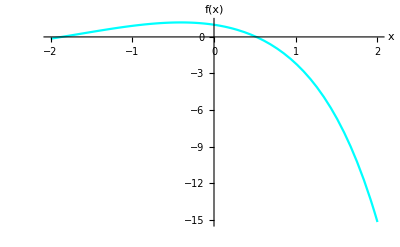

```mathematica
f[x_]=Cos[x]-x*Exp[x]
g[x_]=D[f[x],x]
FindRoot[f[x],{x,1}]
p=0.5;p1=N[p-f[p]/g[p]];
i=0;
If[g[p]==0,
Print["We cannot find the root in the given interval"];];
OutputDetails={{i,p,f[p]}};
While[Abs[f[p]]<0.0005,
i++;
p1=N[p-f[p]/g[p]];
OutputDetails=Append[OutputDetails,{i,p1,f[p1]}];
p=p1];
Print[NumberForm[TableForm[OutputDetails,TableHeadings->{None,{"i","pi","f[pi]"}}],6]];
Plot[f[x],{x,-2,+2},PlotStyle->{Cyan},AxesLabel->{"x","f(x)"}]
```

```mathematica
PRACTICAL 4: GAUSS-JACOBI AND GAUSS-SEIDEL METHOD
```

#### Q1. Jacobi method with stopping condition as no. of iterations.

```mathematica
Clear[A,b,x,n,k,i,m1,m2]
A=N[{{5,1,2},{-3,9,4},{1,2,-7}}];
b={10,-14,-33};
x0={0,0,0};
xk=x0;
m1=Length[A];
m2=Length[b];
n=0;
If[m1≠m2,Print["solution not possible"],OutputDetails={xk};
While[n≤11,
xk1=Table[0,{m1}];
n++;
For[i=1,i≤m1,i++,
xk1[[i]]=(1/A[[i,i]])(b[[i]]-∑_(j=1)^(i-1) A[[i,j]]*xk[[j]]-∑_(j=i+1)^m1 A[[i,j]]*xk[[j]]);];
OutputDetails=Append[OutputDetails,xk1];
xk=xk1;];
colHeading=Table[i,{i,1,m1}];
rowHeading=Table[j,{j,0,n}];
Print[
NumberForm[TableForm[OutputDetails,TableHeadings->{rowHeading,colHeading}],6]];]
Print["Roots after ",n," iterations are ",NumberForm[xk1,9]]
```

| 1 | 2 | 3
0 | 0 | 0 | 0
1 | 2. | -1.55556 | 4.71429
2 | 0.425397 | -2.98413 | 4.55556
3 | 0.774603 | -3.43845 | 3.92245
4 | 1.11871 | -3.04067 | 3.84253
5 | 1.07112 | -2.89044 | 4.00534
6 | 0.975953 | -2.97867 | 4.04146
7 | 0.979148 | -3.02644 | 4.00266
8 | 1.00422 | -3.00813 | 3.98947
9 | 1.00584 | -2.99391 | 3.99828
10 | 0.99947 | -2.99729 | 4.00257
11 | 0.998428 | -3.00132 | 4.0007
12 | 0.999985 | -3.00083 | 3.9994

Roots after 12 iterations are {0.999984588,-3.00083463,3.99939806}

```mathematica
Q2. Seidel method with stopping condition as no.of iterations.
```

```mathematica
Clear[A,b,x,n,m,k,i,m1,m2]
A=N[{{5,1,2},{-3,9,4},{1,2,-7}}];
b={10,-14,-33};
x0={0,0,0};
xk=x0;
m1=Length[A];
m2=Length[b];
n=0;
If[m1≠m2,Print["solution not possible"],OutputDetails={xk};
While[n≤10,
xk1=Table[0,{m1}];
n++;
For[i=1,i≤m1,i++,
xk1[[i]]=(1/A[[i,i]])(b[[i]]-∑_(j=1)^(i-1) A[[i,j]]*xk1[[j]]-∑_(j=i+1)^m1 A[[i,j]]*xk[[j]]);];
OutputDetails=Append[OutputDetails,xk1];
xk=xk1;];
colHeading=Table[i,{i,1,m1}];
rowHeading=Table[j,{j,0,n}];
Print[
NumberForm[TableForm[OutputDetails,TableHeadings->{rowHeading,colHeading}],6]];]
Print["Roots after ",n," iterations are ",NumberForm[xk1,9]]
```

| 1 | 2 | 3
0 | 0 | 0 | 0
1 | 2. | -0.888889 | 4.74603
2 | 0.279365 | -3.57178 | 3.73369
3 | 1.22088 | -2.80801 | 4.08641
4 | 0.927039 | -3.06272 | 3.97166
5 | 1.02388 | -2.97944 | 4.00929
6 | 0.992174 | -3.00674 | 3.99696
7 | 1.00256 | -2.99779 | 4.001
8 | 0.99916 | -3.00072 | 3.99967
9 | 1.00028 | -2.99976 | 4.00011
10 | 0.99991 | -3.00008 | 3.99996
11 | 1.00003 | -2.99997 | 4.00001

Roots after 11 iterations are {1.00002955,-2.99997457,4.00001149}

```mathematica
Q3. Jacobi method with error bound condition.
```

```mathematica
Clear[A,b,x,n,m,k,i,m1,m2]
A=N[{{5,1,2},{-3,9,4},{1,2,-7}}];
b={10,-14,-33};
x0={0,0,0};
xk=x0;
m1=Length[A];
m2=Length[b];
n=0;
If[m1≠m2,Print["solution not possible"],OutputDetails={xk};
MaxNorm=1000;
While[MaxNorm>0.0005,
xk1=Table[0,{m1}];
n++;
For[i=1,i≤m1,i++,
xk1[[i]]=(1/A[[i,i]])(b[[i]]-∑_(j=1)^(i-1) A[[i,j]]*xk[[j]]-∑_(j=i+1)^m1 A[[i,j]]*xk[[j]]);];
OutputDetails=Append[OutputDetails,xk1];
MaxNorm=Max[Abs[xk1-xk]];
xk=xk1;];
colHeading=Table[i,{i,1,m1}];
rowHeading=Table[j,{j,0,n}];
Print[
NumberForm[TableForm[OutputDetails,TableHeadings->{rowHeading,colHeading}],6]];]
Print["Roots after ",MaxNorm>0.0005,"(",n,")"," iterations are ",NumberForm[xk1,9]]
```

| 1 | 2 | 3
0 | 0 | 0 | 0
1 | 2. | -1.55556 | 4.71429
2 | 0.425397 | -2.98413 | 4.55556
3 | 0.774603 | -3.43845 | 3.92245
4 | 1.11871 | -3.04067 | 3.84253
5 | 1.07112 | -2.89044 | 4.00534
6 | 0.975953 | -2.97867 | 4.04146
7 | 0.979148 | -3.02644 | 4.00266
8 | 1.00422 | -3.00813 | 3.98947
9 | 1.00584 | -2.99391 | 3.99828
10 | 0.99947 | -2.99729 | 4.00257
11 | 0.998428 | -3.00132 | 4.0007
12 | 0.999985 | -3.00083 | 3.9994
13 | 1.00041 | -2.99974 | 3.99976
14 | 1.00004 | -2.99976 | 4.00013

Roots after False(14) iterations are {1.00004379,-2.99975714,4.00013321}

```mathematica
Q4.  Seidel method with error bound condition.
```

```mathematica
A=N[{{5,1,2},{-3,9,4},{1,2,-7}}];
b={10,-14,-33};
x0={0,0,0};
xk=x0;
m1=Length[A];
m2=Length[b];
n=0;
If[m1≠m2,Print["Solution not possible"],OutputDetails={xk};
MaxNorm=1000;
While[MaxNorm>0.0005,

xk1=Table[0,{m1}];
n++;
For[i=1,i≤m1,i++,
xk1[[i]]=(1/A[[i,i]])(b[[i]]-∑_(j=1)^(i-1) A[[i,j]]*xk1[[j]]-∑_(j=i+1)^m1 A[[i,j]]*xk[[j]]);];
OutputDetails=Append[OutputDetails,xk1];
MaxNorm=Max[Abs[xk1-xk]];
xk=xk1];
colHeading=Table[i,{i,1,m1}];
rowHeading=Table[j,{j,0,n}];
Print[NumberForm[TableForm[OutputDetails,TableHeadings-> {rowHeading,colHeading}],6]];]
Print["Root after ",MaxNorm>0.0005, "(" ,n, ")" ," iterations are ",NumberForm[xk1,9]]
```

| 1 | 2 | 3
0 | 0 | 0 | 0
1 | 2. | -0.888889 | 4.74603
2 | 0.279365 | -3.57178 | 3.73369
3 | 1.22088 | -2.80801 | 4.08641
4 | 0.927039 | -3.06272 | 3.97166
5 | 1.02388 | -2.97944 | 4.00929
6 | 0.992174 | -3.00674 | 3.99696
7 | 1.00256 | -2.99779 | 4.001
8 | 0.99916 | -3.00072 | 3.99967
9 | 1.00028 | -2.99976 | 4.00011
10 | 0.99991 | -3.00008 | 3.99996

Root after False(10) iterations are {0.999909813,-3.00007762,3.99996494}

```mathematica
Q5. Jacobi method with stopping condition as no.of iterations.
```

```mathematica
Clear[A,b,x,n,m,k,i,m1,m2]
A=N[{{2,1,1},{3,5,2},{2,1,4}}];
b={4,15,8};
x0={0,0,0};
xk=x0;
m1=Length[A];
m2=Length[b];
n=0;
If[m1≠m2,Print["Solution not possible"],OutputDetails={xk};
While[n≤11,
xk1=Table[0,{m1}];
n++;
For[i=1,i≤m1,i++,
xk1[[i]]=(1/A[[i,i]])(b[[i]]-∑_(j=1)^(i-1) A[[i,j]]*xk[[j]]-∑_(j=i+1)^m1 A[[i,j]]*xk[[j]]);];
OutputDetails=Append[OutputDetails,xk1];
xk=xk1;];
colHeading=Table[i,{i,1,m1}];
rowHeading=Table[j,{j,0,n}];
Print[NumberForm[TableForm[OutputDetails,TableHeadings-> {rowHeading,colHeading}],6]];]
Print["Root after ",n," iterations are ",NumberForm[xk1,9]]
```

| 1 | 2 | 3
0 | 0 | 0 | 0
1 | 2. | 3. | 2.
2 | -0.5 | 1. | 0.25
3 | 1.375 | 3.2 | 2.
4 | -0.6 | 1.375 | 0.5125
5 | 1.05625 | 3.155 | 1.95625
6 | -0.555625 | 1.58375 | 0.683125
7 | 0.866562 | 3.06013 | 1.88188
8 | -0.471 | 1.72731 | 0.801687
9 | 0.7355 | 2.96193 | 1.80367
10 | -0.382798 | 1.83723 | 0.891769
11 | 0.6355 | 2.87297 | 1.73209
12 | -0.302531 | 1.92586 | 0.964007

Root after 12 iterations are {-0.302531484,1.92586344,0.964007109}

```mathematica
Q6. Seidel method with stopping condition as no. of iterations.
```

```mathematica
Clear[A,b,x,n,m,k,i,m1,m2]
A=N[{{2,1,1},{3,5,2},{2,1,4}}];
b={4,15,8};
x0={0,0,0};
xk=x0;
m1=Length[A];
m2=Length[b];
n=0;
If[m1≠m2,Print["Solution not possible"],OutputDetails={xk};
While[n≤10,
xk1=Table[0,{m1}];
n++;
For[i=1,i≤m1,i++,
xk1[[i]]=(1/A[[i,i]])(b[[i]]-∑_(j=1)^(i-1) A[[i,j]]*xk1[[j]]-∑_(j=i+1)^m1 A[[i,j]]*xk[[j]]);];
OutputDetails=Append[OutputDetails,xk1];
xk=xk1;];
colHeading=Table[i,{i,1,m1}];
rowHeading=Table[j,{j,0,n}];
Print[NumberForm[TableForm[OutputDetails,TableHeadings-> {rowHeading,colHeading}],6]];]
Print["Root after ",n," iterations are ",NumberForm[xk1,9]]
```

| 1 | 2 | 3
0 | 0 | 0 | 0
1 | 2. | 1.8 | 0.55
2 | 0.825 | 2.285 | 1.01625
3 | 0.349375 | 2.38388 | 1.22934
4 | 0.193391 | 2.39223 | 1.30525
5 | 0.151262 | 2.38714 | 1.32758
6 | 0.142637 | 2.38338 | 1.33284
7 | 0.14189 | 2.38173 | 1.33362
8 | 0.142323 | 2.38116 | 1.33355
9 | 0.142647 | 2.38099 | 1.33343
10 | 0.14279 | 2.38095 | 1.33337
11 | 0.142839 | 2.38095 | 1.33334

Root after 11 iterations are {0.142839332,2.3809498,1.33334288}

```mathematica
Q7. Jacobi method with stopping condition as no. of iterations.
```

```mathematica
Clear[A,b,x,n,m,k,i,m1,m2]
A=N[{{2,-1,1},{2,-3,1},{1,3,-4}}];
b={5,3,4};
x0={0,0,0};
xk=x0;
m1=Length[A];
m2=Length[b];
n=0;
If[m1≠m2,Print["Solution not possible"],OutputDetails={xk};
While[n≤11,
xk1=Table[0,{m1}];
n++;
For[i=1,i≤m1,i++,
xk1[[i]]=(1/A[[i,i]])(b[[i]]-∑_(j=1)^(i-1) A[[i,j]]*xk[[j]]-∑_(j=i+1)^m1 A[[i,j]]*xk[[j]]);];
OutputDetails=Append[OutputDetails,xk1];
xk=xk1;];
colHeading=Table[i,{i,1,m1}];
rowHeading=Table[j,{j,0,n}];
Print[NumberForm[TableForm[OutputDetails,TableHeadings-> {rowHeading,colHeading}],6]];]
Print["Root after ",n," iterations are ",NumberForm[xk1,9]]
```

| 1 | 2 | 3
0 | 0 | 0 | 0
1 | 2.5 | -1. | -1.
2 | 2.5 | 0.333333 | -1.125
3 | 3.22917 | 0.291667 | -0.125
4 | 2.70833 | 1.11111 | 0.0260417
5 | 3.04253 | 0.814236 | 0.510417
6 | 2.65191 | 1.1985 | 0.371311
7 | 2.91359 | 0.89171 | 0.561849
8 | 2.66493 | 1.12968 | 0.397181
9 | 2.86625 | 0.909014 | 0.513491
10 | 2.69776 | 1.082 | 0.398323
11 | 2.84184 | 0.931282 | 0.485937
12 | 2.72267 | 1.05654 | 0.408921

Root after 12 iterations are {2.7226722,1.05653697,0.408920555}

```mathematica
Q8.  Seidel method with stopping condition as no. of iterations.
```

```mathematica
Clear[A,b,x,n,m,k,i,m1,m2]
A=N[{{2,-1,1},{2,-3,1},{1,3,-4}}];
b={5,3,4};
x0={0,0,0};
xk=x0;
m1=Length[A];
m2=Length[b];
n=0;
If[m1≠m2,Print["Solution not possible"],OutputDetails={xk};
While[n≤10,
xk1=Table[0,{m1}];
n++;
For[i=1,i≤m1,i++,
xk1[[i]]=(1/A[[i,i]])(b[[i]]-∑_(j=1)^(i-1) A[[i,j]]*xk1[[j]]-∑_(j=i+1)^m1 A[[i,j]]*xk[[j]]);];
OutputDetails=Append[OutputDetails,xk1];
xk=xk1;];
colHeading=Table[i,{i,1,m1}];
rowHeading=Table[j,{j,0,n}];
Print[NumberForm[TableForm[OutputDetails,TableHeadings-> {rowHeading,colHeading}],6]];]
Print["Root after ",n," iterations are ",NumberForm[xk1,9]]
```

| 1 | 2 | 3
0 | 0 | 0 | 0
1 | 2.5 | 0.666667 | 0.125
2 | 2.77083 | 0.888889 | 0.359375
3 | 2.76476 | 0.962963 | 0.413411
4 | 2.77478 | 0.987654 | 0.434435
5 | 2.77661 | 0.995885 | 0.441066
6 | 2.77741 | 0.998628 | 0.443324
7 | 2.77765 | 0.999543 | 0.44407
8 | 2.77774 | 0.999848 | 0.44432
9 | 2.77776 | 0.999949 | 0.444403
10 | 2.77777 | 0.999983 | 0.444431
11 | 2.77778 | 0.999994 | 0.44444

Root after 11 iterations are {2.77777624,0.999994355,0.444439826}

```mathematica
Q9.  Jacobi method with stopping condition as no.of iterations.
```

```mathematica
Clear[A,b,x,n,m,k,i,m1,m2]
A=N[{{3,-6,2},{4,-1,1},{1,-3,7}}];
b={14,2,22};
x0={0,0,0};
xk=x0;
m1=Length[A];
m2=Length[b];
n=0;
If[m1≠m2,Print["Solution not possible"],OutputDetails={xk};
While[n≤11,
xk1=Table[0,{m1}];
n++;
For[i=1,i≤m1,i++,
xk1[[i]]=(1/A[[i,i]])(b[[i]]-∑_(j=1)^(i-1) A[[i,j]]*xk[[j]]-∑_(j=i+1)^m1 A[[i,j]]*xk[[j]]);];
OutputDetails=Append[OutputDetails,xk1];
xk=xk1;];
colHeading=Table[i,{i,1,m1}];
rowHeading=Table[j,{j,0,n}];
Print[NumberForm[TableForm[OutputDetails,TableHeadings-> {rowHeading,colHeading}],6]];]
Print["Root after ",n," iterations are ",NumberForm[xk1,9]]
```

| 1 | 2 | 3
0 | 0 | 0 | 0
1 | 4.66667 | -2. | 3.14286
2 | -1.42857 | 19.8095 | 1.61905
3 | 43.2063 | -6.09524 | 11.8367
4 | -15.415 | 182.662 | -5.64172
5 | 373.752 | -69.3016 | 83.6288
6 | -189.689 | 1576.64 | -79.951
7 | 3211.24 | -840.707 | 705.943
8 | -2147.38 | 13548.9 | -815.909
9 | 27646.4 | -9407.41 | 6116.59
10 | -22887.9 | 116700. | -7978.09
11 | 238724. | -99531.6 | 53287.2
12 | -234583. | 1.00818×10^6 | -76756.7

Root after 12 iterations are {-234583.422,1.00818108×10^6,-76756.6919}

```mathematica
Q10. Seidel method with stopping condition as no. of iterations.
```

```mathematica
Clear[A,b,x,n,m,k,i,m1,m2]
A=N[{{3,-6,2},{4,-1,1},{1,-3,7}}];
b={14,2,22};
x0={0,0,0};
xk=x0;
m1=Length[A];
m2=Length[b];
n=0;
If[m1≠m2,Print["Solution not possible"],OutputDetails={xk};
While[n≤10,
xk1=Table[0,{m1}];
n++;
For[i=1,i≤m1,i++,
xk1[[i]]=(1/A[[i,i]])(b[[i]]-∑_(j=1)^(i-1) A[[i,j]]*xk1[[j]]-∑_(j=i+1)^m1 A[[i,j]]*xk[[j]]);];
OutputDetails=Append[OutputDetails,xk1];
xk=xk1;];
colHeading=Table[i,{i,1,m1}];
rowHeading=Table[j,{j,0,n}];
Print[NumberForm[TableForm[OutputDetails,TableHeadings-> {rowHeading,colHeading}],6]];]
Print["Root after ",n," iterations are ",NumberForm[xk1,9]]
```

| 1 | 2 | 3
0 | 0 | 0 | 0
1 | 4.66667 | 16.6667 | 9.61905
2 | 31.5873 | 133.968 | 56.0454
3 | 235.24 | 995.004 | 395.967
4 | 1730.7 | 7316.75 | 2891.65
5 | 12710.4 | 53731.3 | 21215.1
6 | 93323.8 | 394508. | 155746.
7 | 685191. | 2.89651×10^6 | 1.14348×10^6
8 | 5.0307×10^6 | 2.12663×10^7 | 8.39545×10^6
9 | 3.69356×10^7 | 1.56138×10^8 | 6.16397×10^7
10 | 2.71182×10^8 | 1.14637×10^9 | 4.52561×10^8
11 | 1.99103×10^9 | 8.41669×10^9 | 3.32272×10^9

Root after 11 iterations are {1.99103135×10^9,8.41668618×10^9,3.32271817×10^9}

```mathematica
PRACTICAL 5(A):SIMPSON METHOD
```

```mathematica
Q1. ∫_0^5 1/(2*x+5)ⅆx,n=10
```

```mathematica
ClearAll[a,b,n,f]
a=0;
b=5;
n=10
h=(b-a)/n;
Print["Value of h =",h]
k=Table[a+ih,{i,1,n}];
f[x_]=1/(2*x+5)
sumodd=0;
sumeven=0;
For[i=1,i<n,i+=2,sumodd+=4*f[x]/.x->k[[i]]];
For[i=2,i<n,i+=2,sumeven+=2*f[x]/.x->k[[i]]];
Sn=(h/3)*((f[x]/.x->a)+N[sumodd]+N[sumeven]+(f[x]/.x->b));
Print["For n=",n," Equal Parts",",Simpson Approximation is : ",Sn]
in=Integrate[1/(2*x+5),{x,0,5}];
Print["Integration of given function from ", a," to ",b,"=",in]
Print["True value is ",in," = ",N[in]]
Print["Absolute error is  |Simpson Approximation-True Value| = ",Abs[Sn-in]]
```

10

Value of h =1/2

1/(5+2 x)

For n=10 Equal Parts,Simpson Approximation is : 1/6 (4/15+28./(5.+2. ih))

Integration of given function from 0 to 5=Log[3]/2

True value is Log[3]/2 = 0.549306

Absolute error is  |Simpson Approximation-True Value| = Abs[1/6 (4/15+28./(5.+2. ih))-Log[3]/2]

```mathematica
Q2.∫_0^0.6 e^(-x^2)ⅆx,h=0.1
```

```mathematica
ClearAll[a,b,n,f]
a=0;
b=0.6;
h=0.1
n=(b-a)/h;
Print["Value of n= ",n]
k=Table[a+i*h,{i,1,n}];
f[x_]=Exp[-x^2]
sumodd=0;
sumeven=0;
For[i=1,i<n,i+=2,sumodd+=4*f[x]/.x->k[[i]]];
For[i=2,i<n,i+=2,sumeven+=2*f[x]/.x->k[[i]]];
Sn=(h/3)*((f[x]/.x->a)+N[sumodd]+N[sumeven]+(f[x]/.x->b));
Print["For n= ",n,"Equal Parts",",Simpson Approximation is : ",Sn]
in=Integrate[Exp[-x^2],{x,0,0.6}];
Print["Integration of given function from ", a," to ",b,"=",in]
Print["True value is ",in," = ",N[in]]
Print["Absolute error is  |Simpson Approximation-True Value| = ",Abs[Sn-in]]
```

0.1

Value of n= 6.

ⅇ^(-x^2)

For n= 6.Equal Parts,Simpson Approximation is : 0.535156

Integration of given function from 0 to 0.6=0.535154

True value is 0.535154 = 0.535154

Absolute error is  |Simpson Approximation-True Value| = 2.13955×10^-6

#### Q3.∫_0^6 1/(1+x^2)ⅆx,n=6

```mathematica
ClearAll[a,b,n,f]
a=0;
b=6;
n=6
h=(b-a)/n;
Print["Value of h =",h]
k=Table[a+i*h,{i,1,n}];
f[x_]=1/(1+x^2)
sumodd=0;
sumeven=0;
For[i=1,i<n,i+=2,sumodd+=4*f[x]/.x->k[[i]]];
For[i=2,i<n,i+=2,sumeven+=2*f[x]/.x->k[[i]]];
Sn=(h/3)*((f[x]/.x->a)+N[sumodd]+N[sumeven]+(f[x]/.x->b));
Print["For n=",n," Equal Parts",",Simpson Approximation is : ",Sn]
in=Integrate[1/(1+x^2),{x,0,6}];
Print["Integration of given function from ", a," to ",b,"=",in]
Print["True value is ",in," = ",N[in]]
Print["Absolute error is  |Simpson Approximation-True Value| = ",Abs[Sn-in]]
```

6

Value of h =1

1/(1+x^2)

For n=6 Equal Parts,Simpson Approximation is : 1.36617

Integration of given function from 0 to 6=ArcTan[6]

True value is ArcTan[6] = 1.40565

Absolute error is  |Simpson Approximation-True Value| = 0.0394742

```mathematica
Q4. ∫_0^1 x^2/(1+x^3)ⅆx,h=0.25
```

```mathematica
ClearAll[a,b,n,f]
a=0;
b=1;
h=0.25
n=(b-a)/h;
Print["Value of n =",n]
k=Table[a+i*h,{i,1,n}];
f[x_]=x^2/(1+x^3)
sumodd=0;
sumeven=0;
For[i=1,i<n,i+=2,sumodd+=4*f[x]/.x->k[[i]]];
For[i=2,i<n,i+=2,sumeven+=2*f[x]/.x->k[[i]]];
Sn=(h/3)*((f[x]/.x->a)+N[sumodd]+N[sumeven]+(f[x]/.x->b));
Print["For n=",n,"Equal Parts",",Simpson Approximation is : ",Sn]
in=Integrate[x^2/(1+x^3),{x,0,1}];
Print["Integration of given function from ", a," to ",b,"=",in]
Print["True value is ",in," = ",N[in]]
Print["Absolute error is  |Simpson Approximation-True Value| = ",Abs[Sn-in]]
```

0.25

Value of n =4.

x^2/(1+x^3)

For n=4.Equal Parts,Simpson Approximation is : 0.231085

Integration of given function from 0 to 1=Log[2]/3

True value is Log[2]/3 = 0.231049

Absolute error is  |Simpson Approximation-True Value| = 0.0000355959

```mathematica
Q5. ∫_0^π sin xⅆx,n=14
```

```mathematica
ClearAll[a,b,n,f]
a=0;
b=π;
n=14
h=(b-a)/n;
Print["Value of h =",h]
k=Table[a+i*h,{i,1,n}];
f[x_]=Sin[x]
sumodd=0;
sumeven=0;
For[i=1,i<n,i+=2,sumodd+=4*f[x]/.x->k[[i]]];
For[i=2,i<n,i+=2,sumeven+=2*f[x]/.x->k[[i]]];
Sn=(h/3)*((f[x]/.x->a)+N[sumodd]+N[sumeven]+(f[x]/.x->b));
Print["For n=",n," Equal Parts",",Simpson Approximation is : ",Sn]
in=Integrate[Sin[x],{x,0,π}];
Print["Integration of given function from ", a," to ",b,"=",in]
Print["True value is ",in," = ",N[in]]
Print["Absolute error is  |Simpson Approximation-True Value| = ",Abs[Sn-in]]
```

14

Value of h =π/14

Sin[x]

For n=14 Equal Parts,Simpson Approximation is : 2.00003

Integration of given function from 0 to π=2

True value is 2 = 2.

Absolute error is  |Simpson Approximation-True Value| = 0.0000283436

```mathematica
Q6. ∫_0^6 e^x/(1+x)ⅆx,n=12
```

```mathematica
ClearAll[a,b,n,f]
a=0;
b=6;
n=12
h=(b-a)/n;
Print["Value of h =",h]
k=Table[a+i*h,{i,1,n}];
f[x_]=Exp[x]/(1+x)
sumodd=0;
sumeven=0;
For[i=1,i<n,i+=2,sumodd+=4*f[x]/.x->k[[i]]];
For[i=2,i<n,i+=2,sumeven+=2*f[x]/.x->k[[i]]];
Sn=(h/3)*((f[x]/.x->a)+N[sumodd]+N[sumeven]+(f[x]/.x->b));
Print["For n=",n," Equal Parts",",Simpson Approximation is : ",Sn]
in=Integrate[Exp[x]/(1+x),{x,0,6}];
Print["Integration of given function from ", a," to ",b,"=",in]
Print["True value is ",in," = ",N[in]]
Print["Absolute error is  |Simpson Approximation-True Value| = ",Abs[Sn-in]]
```

12

Value of h =1/2

ⅇ^x/(1+x)

For n=12 Equal Parts,Simpson Approximation is : 69.7671

Integration of given function from 0 to 6=(-ExpIntegralEi[1]+ExpIntegralEi[7])/ⅇ

True value is (-ExpIntegralEi[1]+ExpIntegralEi[7])/ⅇ = 69.7535

Absolute error is  |Simpson Approximation-True Value| = 0.0136571

```mathematica
PRACTICAL 5(B):TRAPEZOIDAL METHOD
```

```mathematica
Q1.∫_0^5 1/(2+x^2)ⅆx,n=5
```

```mathematica
ClearAll[n,a,b,f]
a=0;
b=5;
n=5
h=(b-a)/n;
Print["Value of h = ",h]
k=Table[a+i*h,{i,1,n}];
sum=0;
f[x]=1/(2+x^2)
For[i=1,i<n,i++,sum+=(2*f[x])/.x->k[[i]]];
Trp=N[(h/2)*(sum+(f[x]/.x->a)+(f[x]/.x->b))];
Print["For n= ",n," Equal Parts",", Trapezoidal Approximation is: ",Trp]
in=Integrate[1/(2+x^2),{x,0,5}];
Print["Integration of given function from ", a, " to ",b," = ",in]
Print["True value is ",in," = ",N[in]]
Print["Absolute error is  |Trapezoidal Approximation-True Value| = ",Abs[Trp-in]]
```

5

Value of h = 1

1/(2+x^2)

For n= 5 Equal Parts, Trapezoidal Approximation is: 0.914983

Integration of given function from 0 to 5 = ArcTan[5/(√2)]/(√2)

True value is ArcTan[5/(√2)]/(√2) = 0.915812

Absolute error is  |Trapezoidal Approximation-True Value| = 0.000828677

```mathematica
Q2. ∫_0^0.6 e^(-x^2)ⅆx,h=0.1
```

```mathematica
ClearAll[n,a,b,f]
a=0;
b=0.6;
h=0.1
n=(b-a)/h;
Print["Value of n = ",n]
k=Table[a+i*h,{i,1,n}];
sum=0;
f[x]=Exp[-x^2]
For[i=1,i<n,i++,sum+=(2*f[x])/.x->k[[i]]];
Trp=N[(h/2)*(sum+(f[x]/.x->a)+(f[x]/.x->b))];
Print["For n= ",n ," Equal Parts",", Trapezoidal Approximation is: ",Trp]
in=Integrate[Exp[-x^2],{x,0,0.6}];
Print["Integration of given function from ", a, " to ",b," = ",in]
Print["True value is ",in," = ",N[in]]
Print["Absolute error is  |Trapezoidal Approximation-True Value| = ",Abs[Trp-in]]
```

0.1

Value of n = 6.

ⅇ^(-x^2)

For n= 6. Equal Parts, Trapezoidal Approximation is: 0.534455

Integration of given function from 0 to 0.6 = 0.535154

True value is 0.535154 = 0.535154

Absolute error is  |Trapezoidal Approximation-True Value| = 0.000698207

For n= 6.Equal Parts, Trapezoidal Approximation is: 0.534455

Integration of given function from 0 to 0.6 = 0.535154

True value is 0.535154 = 0.535154

Absolute error is  |Trapezoidal Approximation-True Value| = 0.000698207

#### Q3. ∫_0^6 1/(1+x^2)ⅆx,n=6

```mathematica
ClearAll[n,a,b,f]
a=0;
b=6;
n=6
h=(b-a)/n;
Print["Value of h = ",h]
k=Table[a+i*h,{i,1,n}];
sum=0;
f[x]=1/(1+x^2)
For[i=1,i<n,i++,sum+=(2*f[x])/.x->k[[i]]];
Trp=N[(h/2)*(sum+(f[x]/.x->a)+(f[x]/.x->b))];
Print["For n= ",n ," Equal Parts",", Trapezoidal Approximation is: ",Trp]
in=Integrate[1/(1+x^2),{x,0,6}];
Print["Integration of given function from ", a, " to ",b," = ",in]
Print["True value is ",in," = ",N[in]]
Print["Absolute error is  |Trapezoidal Approximation-True Value| = ",Abs[Trp-in]]
```

6

Value of h = 1

1/(1+x^2)

For n= 6 Equal Parts, Trapezoidal Approximation is: 1.4108

Integration of given function from 0 to 6 = ArcTan[6]

True value is ArcTan[6] = 1.40565

Absolute error is  |Trapezoidal Approximation-True Value| = 0.00515093

```mathematica
Q4. ∫_0^1 x^2/(1+x^3)ⅆx,h=0.25
```

```mathematica
ClearAll[n,a,b,f]
a=0;
b=1;
h=0.25
n=(b-a)/h;
Print["Value of n = ",n]
k=Table[a+i*h,{i,1,n}];
sum=0;
f[x]=x^2/(1+x^3)
For[i=1,i<n,i++,sum+=(2*f[x])/.x->k[[i]]];
Trp=N[(h/2)*(sum+(f[x]/.x->a)+(f[x]/.x->b))];
Print["For n= ",n ," Equal Parts",", Trapezoidal Approximation is: ",Trp]
in=Integrate[x^2/(1+x^3),{x,0,1}];
Print["Integration of given function from ", a, " to ",b," = ",in]
Print["True value is ",in," = ",N[in]]
Print["Absolute error is  |Trapezoidal Approximation-True Value| = ",Abs[Trp-in]]
```

0.25

Value of n = 4.

x^2/(1+x^3)

For n= 4. Equal Parts, Trapezoidal Approximation is: 0.232341

Integration of given function from 0 to 1 = Log[2]/3

True value is Log[2]/3 = 0.231049

Absolute error is  |Trapezoidal Approximation-True Value| = 0.00129221

#### Q5. ∫_0^π sinxⅆx,n=11

```mathematica
ClearAll[n,a,b,f]
a=0;
b=π;
n=11
h=(b-a)/n;
Print["Value of h = ",h]
k=Table[a+i*h,{i,1,n}];
sum=0;
f[x]=Sin[x]
For[i=1,i<n,i++,sum+=(2*f[x])/.x->k[[i]]];
Trp=N[(h/2)*(sum+(f[x]/.x->a)+(f[x]/.x->b))];
Print["For n= ",n ," Equal Parts",", Trapezoidal Approximation is: ",Trp]
in=Integrate[Sin[x],{x,0,π}];
Print["Integration of given function from ", a, " to ",b," = ",in]
Print["True value is ",in," = ",N[in]]
Print["Absolute error is  |Trapezoidal Approximation-True Value| = ",Abs[Trp-in]]
```

11

Value of h = π/11

Sin[x]

For n= 11 Equal Parts, Trapezoidal Approximation is: 1.98639

Integration of given function from 0 to π = 2

True value is 2 = 2.

Absolute error is  |Trapezoidal Approximation-True Value| = 0.013613

```mathematica
Q6. ∫_0^6 e^x/(1+x)ⅆx,n=12
```

```mathematica
ClearAll[n,a,b,f]
a=0;
b=6;
n=12
h=(b-a)/n;
Print["Value of h = ",h]
k=Table[a+i*h,{i,1,n}];
sum=0;
f[x]=Exp[x]/(1+x)
For[i=1,i<n,i++,sum+=(2*f[x])/.x->k[[i]]];
Trp=N[(h/2)*(sum+(f[x]/.x->a)+(f[x]/.x->b))];
Print["For n= ",n,"Equal Parts",", Trapezoidal Approximation is: ",Trp]
in=Integrate[Exp[x]/(1+x),{x,0,6}];
Print["Integration of given function from ", a, " to ",b," = ",in]
Print["True value is ",in," = ",N[in]]
Print["Absolute error is  |Trapezoidal Approximation-True Value| = ",Abs[Trp-in]]
```

12

Value of h = 1/2

ⅇ^x/(1+x)

For n= 12Equal Parts, Trapezoidal Approximation is: 70.7791

Integration of given function from 0 to 6 = (-ExpIntegralEi[1]+ExpIntegralEi[7])/ⅇ

True value is (-ExpIntegralEi[1]+ExpIntegralEi[7])/ⅇ = 69.7535

Absolute error is  |Trapezoidal Approximation-True Value| = 1.02563

```mathematica
PRACTICAL 6:LAGRANGE AND NEWTON 
DIVIDED DIFFERENCE METHOD
```

#### Q1.Find the Lagrange’s form of Interpolating Polynomial for the given function or function data: a)(-1,5),(0,1),(1,1),(2,11)

```mathematica
xi ={- 1,0,1,2};
fi={5,1,1,11};
n=Length[xi];
For[k=1,k≤n,k++,
Subscript[L, k][x_]=(∏_(j=1)^(k-1) (x-xi[[j]])/(xi[[k]]-xi[[j]]))*(∏_(j=k+1)^n (x-xi[[j]])/(xi[[k]]-xi[[j]]))];
p[x_]=∑_(k=1)^n Subscript[L, k][x]*fi[[k]];
Print["Lagrange polynomial p(x)=", p[x]]
Print["Simplified polynomial p(x)=", Simplify[p[x]]]
Print["Approximate value of f at x=1.5 is ", p[1.5]]
```

Lagrange polynomial p(x)=-5/6 (1-x) (2-x) x+1/2 (1-x) (2-x) (1+x)+1/2 (2-x) x (1+x)+11/6 (-1+x) x (1+x)

Simplified polynomial p(x)=1-3 x+2 x^2+x^3

Approximate value of f at x=1.5 is 4.375

#### b) f(x)=ln(x),x=1,2,3

```mathematica
Clear[x,k,f,L,p]
xi ={1,2,3};
f[x_]:=Log[x];
n=Length[xi];
For[k=1,k≤n,k++,
Subscript[L, k][x_]=(∏_(j=1)^(k-1) (x-xi[[j]])/(xi[[k]]-xi[[j]]))*(∏_(j=k+1)^n (x-xi[[j]])/(xi[[k]]-xi[[j]]))];
p[x_]=∑_(k=1)^n Subscript[L, k][x]*N[f[xi[[k]]]];


Print["Lagrange polynomial p(x)=", p[x]]
Print["Simplified polynomial p(x)=", Simplify[p[x]]]
Print["Approximate value of f at x=1.5 is ", p[1.5]]
```

Lagrange polynomial p(x)=0.+0.693147 (3-x) (-1+x)+0.549306 (-2+x) (-1+x)

Simplified polynomial p(x)=-0.980829+1.12467 x-0.143841 x^2

Approximate value of f at x=1.5 is 0.382534

#### Q2. Find the Newton’s divided difference form of Interpolating Polynomial for the given function or function data:

#### a) (-1, 5), (0, 1), (1, 1), (2, 11)

```mathematica
Clear[g,f,k,n,i,k,p,x,h,s]
xi={-1,0,1,2};
fi={5,1,1,11};
n=Length[xi];
g[0]=fi;
s[0,x_]=1;
For[k=1,k≤n-1,k++,
g[k]=Table[(g[k-1][[j]]-g[k-1][[j-1]])/(xi[[j+k-1]]-xi[[j-1]]),{j,2,n-k+1}];(*Table of y values*)
s[k,x_]=s[k-1,x]*(x-xi[[k]])](*f(x)=f(Subscript[x, 0])+(x-Subscript[x, 0])[Subscript[x, 0],Subscript[x, 1]]+(x-Subscript[x, 0])(x-Subscript[x, 1])[Subscript[x, 0],Subscript[x, 1],Subscript[x, 2]]+_________(x-Subscript[x, n-1])[Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],___ Subscript[_x, n]]*)
p[x_]:=∑_(i=0)^(n-1) g[i][[1]]*s[i,x](*f(x)=f(Subscript[x, 0])+(x-Subscript[x, 0])[Subscript[x, 0],Subscript[x, 1]]+(x-Subscript[x, 0])(x-Subscript[x, 1])[Subscript[x, 0],Subscript[x, 1],Subscript[x, 2]]+_________(x-Subscript[x, n-1])[Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],___ Subscript[_x, n]]*)
Print["Newton's Divided Difference polynomial p(x)=", p[x]]
h[x_]:=Simplify[p[x]];
Print["Simplified polnomial p(x)=", h[x]]
Print["Approximate value of f at x=1.5 is ", p[1.5]]
```

Newton's Divided Difference polynomial p(x)=5-4 (1+x)+2 x (1+x)+(-1+x) x (1+x)

Simplified polnomial p(x)=1-3 x+2 x^2+x^3

Approximate value of f at x=1.5 is 4.375

#### b) f (x) = ln (x), x = 1, 2, 3

```mathematica
Clear[g,f,k,n,i,k,p,x,h,s]
xi={1,2,3};
n=Length[xi];
f[x_]:=Log[x]
fi=Table[N[f[xi[[i]]]],{i,1,n}];
g[0]=fi;
s[0,x_]=1;
For[k=1,k≤n-1,k++,
g[k]=Table[(g[k-1][[j]]-g[k-1][[j-1]])/(xi[[j+k-1]]-xi[[j-1]]),{j,2,n-k+1}];
s[k,x_]=s[k-1,x]*(x-xi[[k]])]
p[x_]:=∑_(i=0)^(n-1) g[i][[1]]*s[i,x]
Print["Newton's Divided Difference polynomial p(x)=", p[x]]
h[x_]:=Simplify[p[x]];
Print["Simplified polnomial p(x)=", h[x]]
Print["Approximate value of f at x=1.5 is ", p[1.5]]
```

Newton's Divided Difference polynomial p(x)=0.+0.693147 (-1+x)-0.143841 (-2+x) (-1+x)

Simplified polnomial p(x)=-0.980829+1.12467 x-0.143841 x^2

Approximate value of f at x=1.5 is 0.382534

#### Q3. Find the Lagrange’s form of Interpolating Polynomial for the given function or function data:

```mathematica
a) f(x)=sin(x),x=0,π/4,π/2
```

```mathematica
Clear[x,k,f,L,p]
xi ={0,π/4,π/2};
f[x_]:=Sin[x];
n=Length[xi];
For[k=1,k≤n,k++,
Subscript[L, k][x_]=(∏_(j=1)^(k-1) (x-xi[[j]])/(xi[[k]]-xi[[j]]))*(∏_(j=k+1)^n (x-xi[[j]])/(xi[[k]]-xi[[j]]))];
p[x_]=∑_(k=1)^n Subscript[L, k][x]*N[f[xi[[k]]]];
Print["Lagrange polynomial p(x)=", p[x]]
Print["Simplified polynomial p(x)=", Simplify[p[x]]]
Print["Approximate value of f at x=π/6 is ", p[π/6]]
```

Lagrange polynomial p(x)=0.-1.14632 x (-π/2+x)+0.810569 x (-π/4+x)

Simplified polynomial p(x)=0.+1.16401 x-0.335749 x^2

Approximate value of f at x=π/6 is 0.517428

#### b) (0,1),(1,2),(2,4),(3,8)

```mathematica
xi ={0,1,2,3};
fi={1,2,4,8};
n=Length[xi];
For[k=1,k≤n,k++,
Subscript[L, k][x_]=(∏_(j=1)^(k-1) (x-xi[[j]])/(xi[[k]]-xi[[j]]))*(∏_(j=k+1)^n (x-xi[[j]])/(xi[[k]]-xi[[j]]))];
p[x_]=∑_(k=1)^n Subscript[L, k][x]*fi[[k]];
Print["Lagrange polynomial p(x)=", p[x]]
Print["Simplified polynomial p(x)=", Simplify[p[x]]]
Print["Approximate value of f at x=3.5 is ", p[3.5]]
```

Lagrange polynomial p(x)=1/6 (1-x) (2-x) (3-x)+(2-x) (3-x) x+2 (3-x) (-1+x) x+4/3 (-2+x) (-1+x) x

Simplified polynomial p(x)=1/6 (6+5 x+x^3)

Approximate value of f at x=3.5 is 11.0625

#### Q4. Find the Newton’s divided difference form of Interpolating Polynomial for the given function or function data:

#### a) f(x)=sin(x),x=0,π/4,π/2

```mathematica
Clear[g,f,k,n,i,k,p,x,h,s]
xi={0,π/4,π/2};
n=Length[xi];
f[x_]:=Sin[x]
fi=Table[N[f[xi[[i]]]],{i,1,n}];
g[0]=fi;
s[0,x_]=1;
For[k=1,k≤n-1,k++,
g[k]=Table[(g[k-1][[j]]-g[k-1][[j-1]])/(xi[[j+k-1]]-xi[[j-1]]),{j,2,n-k+1}];
s[k,x_]=s[k-1,x]*(x-xi[[k]])]
p[x_]:=∑_(i=0)^(n-1) g[i][[1]]*s[i,x]
Print["Newton's Divided Difference polynomial p(x)=", p[x]]
h[x_]:=Simplify[p[x]];
Print["Simplified polnomial p(x)=", h[x]]
Print["Approximate value of f at x=π/6 is ", p[π/6]]
```

Newton's Divided Difference polynomial p(x)=0.+0.900316 x-0.335749 x (-π/4+x)

Simplified polnomial p(x)=0.+1.16401 x-0.335749 x^2

Approximate value of f at x=π/6 is 0.517428

#### b) (0,1),(1,2),(2,4),(3,8)

```mathematica
Clear[g,f,k,n,i,k,p,x,h,s]
xi={0,1,2,3};
fi={1,2,4,8};
n=Length[xi];
g[0]=fi;
s[0,x_]=1;
For[k=1,k≤n-1,k++,
g[k]=Table[(g[k-1][[j]]-g[k-1][[j-1]])/(xi[[j+k-1]]-xi[[j-1]]),{j,2,n-k+1}];
s[k,x_]=s[k-1,x]*(x-xi[[k]])]
p[x_]:=∑_(i=0)^(n-1) g[i][[1]]*s[i,x]
Print["Newton's Divided Difference polynomial p(x)=", p[x]]
h[x_]:=Simplify[p[x]];
Print["Simplified polnomial p(x)=", h[x]]
Print["Approximate value of f at x=3.5 is ", p[3.5]]
```

Newton's Divided Difference polynomial p(x)=1+x+1/2 (-1+x) x+1/6 (-2+x) (-1+x) x

Simplified polnomial p(x)=1/6 (6+5 x+x^3)

Approximate value of f at x=3.5 is 11.0625

```mathematica
PRACTICAL 7:EULER'S METHOD
```

#### Q1. Using Euler method find the appropriate solution for the initial value problem y’[x]=x-2y, 0≤x≤1 , y[0]=1 and use number of iterations, n=10

```mathematica
Clear[a,b,n,h,x,y,i,j]
f[x_,y_]:=x-2*y;
a=0;
b=1;
n=10;
h=(b-a)/n;
x[0]=0;y[0]=1;
Print["Value of h = ",N[h]]
For[i=1,i<n+1,i++,x[i]=N[a+i+h];
y[i]=y[i-1]+h*f[x[i-1],y[i-1]];
Print["For x[",i,"]=",x[i],"value of y[",x[i],"]=" ,N[y[i]]]]
```

Value of h = 0.1

For x[1]=1.1value of y[1.1]=0.8

For x[2]=2.1value of y[2.1]=0.75

For x[3]=3.1value of y[3.1]=0.81

For x[4]=4.1value of y[4.1]=0.958

For x[5]=5.1value of y[5.1]=1.1764

For x[6]=6.1value of y[6.1]=1.45112

For x[7]=7.1value of y[7.1]=1.7709

For x[8]=8.1value of y[8.1]=2.12672

For x[9]=9.1value of y[9.1]=2.51137

For x[10]=10.1value of y[10.1]=2.9191

#### Q2. Using Euler method find the approximate solution for the initial value problem y’[x]= x^2+y^2 , 0≤x≤1 , y[0]=1 and use number of iterations, n=12

```mathematica
Clear[a,b,n,h,y,i,j]
f[x_,y_]:=x^2+y^2;
a=0;
b=1;
n=12;
h=(b-a)/n;x[0]=0;y[0]=1;
Print["Value of h = ",N[h]]
For[i=1,i<n+1,i++,x[i]=N[a+i*h];
y[i]=y[i-1]+h*f[x[i-1],y[i-1]];
Print["For x[",i,"]=",x[i]," value of y[",x[i],"]= ",N[y[i]]]]
```

Value of h = 0.0833333

For x[1]=0.0833333 value of y[0.0833333]= 1.08333

For x[2]=0.166667 value of y[0.166667]= 1.18171

For x[3]=0.25 value of y[0.25]= 1.3004

For x[4]=0.333333 value of y[0.333333]= 1.44653

For x[5]=0.416667 value of y[0.416667]= 1.63016

For x[6]=0.5 value of y[0.5]= 1.86607

For x[7]=0.583333 value of y[0.583333]= 2.17709

For x[8]=0.666667 value of y[0.666667]= 2.60043

For x[9]=0.75 value of y[0.75]= 3.20098

For x[10]=0.833333 value of y[0.833333]= 4.10171

For x[11]=0.916667 value of y[0.916667]= 5.56159

For x[12]=1. value of y[1.]= 8.20922

#### Q3. Using Euler method find the approximate solution for the initial value problem y’[x]=1+y/x, 1≤x≤6 , y[1]= 1 and use number of iterations,n=10

```mathematica
Clear[a,b,n,h,y,i,j]
f[x_,y_]:=1+y/x;
a=1;
b=6;
n=10;
h=(b-a)/n;x[0]=1;y[0]=1;
Print["Value of h = ",N[h]]
For[i=1,i<n+1,i++,x[i]=N[a+i*h];
y[i]=y[i-1]+h*f[x[i-1],y[i-1]];
Print["For x[",i,"]=",x[i]," value of y[",x[i],"]= ",N[y[i]]]]
```

#### Q4. Find y corresponding to x=1,Given that dy/dx=x+y and y=1 when x=0, take n=10.

```mathematica
Clear[a,b,n,h,y,i,j]
f[x_,y_]:=x+y;
a=0;
b=1;
n=10;
h=(b-a)/n;x[0]=0;y[0]=1;
Print["Value of h = ",N[h]]
For[i=1,i<n+1,i++,x[i]=N[a+i*h];
y[i]=y[i-1]+h*f[x[i-1],y[i-1]];
Print["For x[",i,"]=",x[i]," value of y[",x[i],"]= ",N[y[i]]]]
```

Value of h = 0.1

For x[1]=0.1 value of y[0.1]= 1.1

For x[2]=0.2 value of y[0.2]= 1.22

For x[3]=0.3 value of y[0.3]= 1.362

For x[4]=0.4 value of y[0.4]= 1.5282

For x[5]=0.5 value of y[0.5]= 1.72102

For x[6]=0.6 value of y[0.6]= 1.94312

For x[7]=0.7 value of y[0.7]= 2.19743

For x[8]=0.8 value of y[0.8]= 2.48718

For x[9]=0.9 value of y[0.9]= 2.8159

For x[10]=1. value of y[1.]= 3.18748

#### Q5. Find y(1) with 10 iterations, dy/dx = x^2+y^2 with y(0)=1.

```mathematica
Clear[a,b,n,h,y,i,j]
f[x_,y_]:=x^2+y^2;
a=0;
b=1;
n=10;
h=(b-a)/n;x[0]=0;y[0]=1;
Print["Value of h = ",N[h]]
For[i=1,i<n+1,i++,x[i]=N[a+i*h];
y[i]=y[i-1]+h*f[x[i-1],y[i-1]];
Print["For x[",i,"]=",x[i]," value of y[",x[i],"]= ",N[y[i]]]]
```

Value of h = 0.1

For x[1]=0.1 value of y[0.1]= 1.1

For x[2]=0.2 value of y[0.2]= 1.222

For x[3]=0.3 value of y[0.3]= 1.37533

For x[4]=0.4 value of y[0.4]= 1.57348

For x[5]=0.5 value of y[0.5]= 1.83707

For x[6]=0.6 value of y[0.6]= 2.19955

For x[7]=0.7 value of y[0.7]= 2.71935

For x[8]=0.8 value of y[0.8]= 3.50783

For x[9]=0.9 value of y[0.9]= 4.80232

For x[10]=1. value of y[1.]= 7.18955

#### Q6. Find y(0.3), dy/dx=3x+2y with y(0)=1,take h=0.1 .

```mathematica
Clear[a,b,n,h,y,i,j]
f[x_,y_]:=3x+2y;
a=0;
b=0.3;
h=0.1;
n=(b-a)/h;x[0]=0;y[0]=1;
Print["Value of n = ",N[n]]
For[i=1,i<n+1,i++,x[i]=N[a+i*h];
y[i]=y[i-1]+h*f[x[i-1],y[i-1]];
Print["For x[",i,"]=",x[i]," value of y[",x[i],"]= ",N[y[i]]]]
```

Value of n = 3.

For x[1]=0.1 value of y[0.1]= 1.2

For x[2]=0.2 value of y[0.2]= 1.47

For x[3]=0.3 value of y[0.3]= 1.824

```mathematica
PRACTICAL 8(A): ELIMINATION METHOD
```

#### Q1. Solve x + 10 y + 100 z + 1000 w = 227.04 x + 15 y + 225 z + 3375 w = 362.78 x + 20 y + 400 z + 8000 w = 517.35 x + 22.5 y + 506.25 z + 11391 w = 602.97

```mathematica
Clear[A,b,i,k,j,c,x,m]
A={{1,10,100,1000},{1,15,225,3375},{1,20,400,8000},{1,22.5,506.25,11391}};
A//MatrixForm
b={227.04,362.78,517.35,602.97}
b//MatrixForm
m1=Length[A]
m2=Length[b]
x=Table[0,{m1}]
If[m1≠ m2,Print["The system cannot be solved"],
Table[AppendTo[A[[i]],b[[i]]],{i,m1}]; Print["[A|b] =",A//MatrixForm]
For[i=1,i≤ m1-1,i++,s=Abs[A[[i,i]]];c=i;
For[j=i+1,j≤ m1,j++,If[Abs[A[[j,i]]]>s,s=A[[j,i]];c=j;]];
For[k=1,k≤ m1+1,k++,d[k]=A[[i,k]];A[[i,k]]=A[[c,k]];A[[c,k]]=d[k]];
Print ["Step=",i ,A//MatrixForm];
For [j=i+1,j≤m1,j++,m=A[[j,i]]/A[[i,i]];
For[k=1,k≤m1+1,k++,A[[j,k]]=A[[j,k]]-(m*A[[i,k]])];];
Print[A//MatrixForm];];
For[i=0,i≤m1-1,i++,x[[m1-i]]=(A[[m1-i,m1+1]]-Sum[A[[m1-i,j]]*x[[j]],{j,m1-i+1,m1}])/A[[m1-i,m1-i]];];Print["x= ",x//MatrixForm];]
```

(1 | 10 | 100 | 1000
1 | 15 | 225 | 3375
1 | 20 | 400 | 8000
1 | 22.5 | 506.25 | 11391)

(227.04
362.78
517.35
602.97)

4

4

{0,0,0,0}

[A|b] =(1 | 10 | 100 | 1000 | 227.04
1 | 15 | 225 | 3375 | 362.78
1 | 20 | 400 | 8000 | 517.35
1 | 22.5 | 506.25 | 11391 | 602.97)

Step=1(1 | 10 | 100 | 1000 | 227.04
1 | 15 | 225 | 3375 | 362.78
1 | 20 | 400 | 8000 | 517.35
1 | 22.5 | 506.25 | 11391 | 602.97)

(1 | 10 | 100 | 1000 | 227.04
0 | 5 | 125 | 2375 | 135.74
0 | 10 | 300 | 7000 | 290.31
0 | 12.5 | 406.25 | 10391 | 375.93)

Step=2(1 | 10 | 100 | 1000 | 227.04
0 | 12.5 | 406.25 | 10391 | 375.93
0 | 10 | 300 | 7000 | 290.31
0 | 5 | 125 | 2375 | 135.74)

(1 | 10 | 100 | 1000 | 227.04
0 | 12.5 | 406.25 | 10391 | 375.93
0. | 0. | -25. | -1312.8 | -10.434
0. | 0. | -37.5 | -1781.4 | -14.632)

Step=3(1 | 10 | 100 | 1000 | 227.04
0 | 12.5 | 406.25 | 10391 | 375.93
0. | 0. | -37.5 | -1781.4 | -14.632
0. | 0. | -25. | -1312.8 | -10.434)

(1 | 10 | 100 | 1000 | 227.04
0 | 12.5 | 406.25 | 10391 | 375.93
0. | 0. | -37.5 | -1781.4 | -14.632
0. | 0. | 3.55271×10^-15 | -125.2 | -0.679333)

x= (-4.22796
21.2599
0.132431
0.00542599)

```mathematica
Clear[A,b]
A={{1,10,100,1000},{1,15,225,3375},{1,20,400,8000},{1,22.5,506.25,11391}};
A//MatrixForm
b={227.04,362.78,517.35,602.97};
b//MatrixForm
Print["Exactsol= ",LinearSolve[A,b]//MatrixForm]
```

(1 | 10 | 100 | 1000
1 | 15 | 225 | 3375
1 | 20 | 400 | 8000
1 | 22.5 | 506.25 | 11391)

(227.04
362.78
517.35
602.97)

Exactsol= (-4.22796
21.2599
0.132431
0.00542599)

#### Q2. Solve: 2 x_1 + x_2 + x_3 = 4 3 x_1 + 5 x_2 + 2 x_3 = 15 2 x_1 + x_2 + 4 x_3 = 8

```mathematica
Clear[A,b,i,k,j,c,x,m]
A={{2,1,1},{3,5,2},{2,1,4}};
A//MatrixForm
b={4,15,8}
b//MatrixForm
m1=Length[A]
m2=Length[b]
x=Table[0,{m1}]
If[m1≠ m2,Print["The system cannot be solved"],
Table[AppendTo[A[[i]],b[[i]]],{i,m1}]; Print["[A|b] =",A//MatrixForm]
For[i=1,i≤ m1-1,i++,s=Abs[A[[i,i]]];c=i;
For[j=i+1,j≤ m1,j++,If[Abs[A[[j,i]]]>s,s=A[[j,i]];c=j;]];
For[k=1,k≤ m1+1,k++,d[k]=A[[i,k]];A[[i,k]]=A[[c,k]];A[[c,k]]=d[k]];
Print ["Step=",i ,A//MatrixForm];
For [j=i+1,j≤m1,j++,m=A[[j,i]]/A[[i,i]];
For[k=1,k≤m1+1,k++,A[[j,k]]=A[[j,k]]-(m*A[[i,k]])];];
Print[A//MatrixForm];];
For[i=0,i≤m1-1,i++,x[[m1-i]]=(A[[m1-i,m1+1]]-Sum[A[[m1-i,j]]*x[[j]],{j,m1-i+1,m1}])/A[[m1-i,m1-i]];];Print["x= ",x//MatrixForm];]
```

(2 | 1 | 1
3 | 5 | 2
2 | 1 | 4)

(4
15
8)

3

3

{0,0,0}

[A|b] =(2 | 1 | 1 | 4
3 | 5 | 2 | 15
2 | 1 | 4 | 8)

Step=1(3 | 5 | 2 | 15
2 | 1 | 1 | 4
2 | 1 | 4 | 8)

(3 | 5 | 2 | 15
0 | -7/3 | -1/3 | -6
0 | -7/3 | 8/3 | -2)

Step=2(3 | 5 | 2 | 15
0 | -7/3 | -1/3 | -6
0 | -7/3 | 8/3 | -2)

(3 | 5 | 2 | 15
0 | -7/3 | -1/3 | -6
0 | 0 | 3 | 4)

x= (1/7
50/21
4/3)

```mathematica
Clear[A,b]
A={{2,1,1},{3,5,2},{2,1,4}};
A//MatrixForm
b={4,15,8};
b//MatrixForm
Print["Exactsol= ",LinearSolve[A,b]//MatrixForm]
```

(2 | 1 | 1
3 | 5 | 2
2 | 1 | 4)

(4
15
8)

Exactsol= (1/7
50/21
4/3)

#### Q3. Solve: 2 x_1 - x_2 + x_3 = 5 2 x_1 - 3 x_2 + x_3 = 3 x_1 + 3 x_2 - 4 x_3 = 4

```mathematica
Clear[A,b,i,k,j,c,x,m]
A={{2,-1,1},{2,-3,1},{1,3,-4}};
A//MatrixForm
b={5,3,4}
b//MatrixForm
m1=Length[A]
m2=Length[b]
x=Table[0,{m1}]
If[m1≠ m2,Print["The system cannot be solved"],
Table[AppendTo[A[[i]],b[[i]]],{i,m1}]; Print["[A|b] =",A//MatrixForm]
For[i=1,i≤ m1-1,i++,s=Abs[A[[i,i]]];c=i;
For[j=i+1,j≤ m1,j++,If[Abs[A[[j,i]]]>s,s=A[[j,i]];c=j;]];
For[k=1,k≤ m1+1,k++,d[k]=A[[i,k]];A[[i,k]]=A[[c,k]];A[[c,k]]=d[k]];
Print ["Step=",i  ,A//MatrixForm];
For [j=i+1,j≤m1,j++,m=A[[j,i]]/A[[i,i]];
For[k=1,k≤m1+1,k++,A[[j,k]]=A[[j,k]]-(m*A[[i,k]])];];
Print[A//MatrixForm];];
For[i=0,i≤m1-1,i++,x[[m1-i]]=(A[[m1-i,m1+1]]-Sum[A[[m1-i,j]]*x[[j]],{j,m1-i+1,m1}])/A[[m1-i,m1-i]];];Print["x= ",x//MatrixForm];]
```

(2 | -1 | 1
2 | -3 | 1
1 | 3 | -4)

(5
3
4)

3

3

{0,0,0}

[A|b] =(2 | -1 | 1 | 5
2 | -3 | 1 | 3
1 | 3 | -4 | 4)

Step=1(2 | -1 | 1 | 5
2 | -3 | 1 | 3
1 | 3 | -4 | 4)

(2 | -1 | 1 | 5
0 | -2 | 0 | -2
0 | 7/2 | -9/2 | 3/2)

Step=2(2 | -1 | 1 | 5
0 | 7/2 | -9/2 | 3/2
0 | -2 | 0 | -2)

(2 | -1 | 1 | 5
0 | 7/2 | -9/2 | 3/2
0 | 0 | -18/7 | -8/7)

x= (25/9
1
4/9)

```mathematica
Clear[A,b]
A={{2,-1,1},{2,-3,1},{1,3,-4}};
A//MatrixForm
b={5,3,4};
b//MatrixForm
Print["Exactsol= ",LinearSolve[A,b]//MatrixForm]
```

(2 | -1 | 1
2 | -3 | 1
1 | 3 | -4)

(5
3
4)

Exactsol= (25/9
1
4/9)

#### Q4. Solve: 3 x_1 - 6 x_2 + 2 x_3 = 14 4 x_1 - x_2 + x_3 = 2 x_1 - 3 x_2 + 7 x_3 = 22

```mathematica
Clear[A,b,i,k,j,c,x,m]
A={{3,-6,2},{4,-1,1},{1,-3,7}};
A//MatrixForm
b={14,2,22}
b//MatrixForm
m1=Length[A]
m2=Length[b]
x=Table[0,{m1}]
If[m1≠ m2,Print["The system cannot be solved"],
Table[AppendTo[A[[i]],b[[i]]],{i,m1}]; Print["[A|b] =",A//MatrixForm]
For[i=1,i≤ m1-1,i++,s=Abs[A[[i,i]]];c=i;
For[j=i+1,j≤ m1,j++,If[Abs[A[[j,i]]]>s,s=A[[j,i]];c=j;]];
For[k=1,k≤ m1+1,k++,d[k]=A[[i,k]];A[[i,k]]=A[[c,k]];A[[c,k]]=d[k]];
Print ["Step=",i ,A//MatrixForm];
For [j=i+1,j≤m1,j++,m=A[[j,i]]/A[[i,i]];
For[k=1,k≤m1+1,k++,A[[j,k]]=A[[j,k]]-(m*A[[i,k]])];];
Print[A//MatrixForm];];
For[i=0,i≤m1-1,i++,x[[m1-i]]=(A[[m1-i,m1+1]]-Sum[A[[m1-i,j]]*x[[j]],{j,m1-i+1,m1}])/A[[m1-i,m1-i]];];Print["x= ",x//MatrixForm];]
```

(3 | -6 | 2
4 | -1 | 1
1 | -3 | 7)

{14,2,22}

(14
2
22)

3

3

{0,0,0}

[A|b] =(3 | -6 | 2 | 14
4 | -1 | 1 | 2
1 | -3 | 7 | 22)

Step=1(4 | -1 | 1 | 2
3 | -6 | 2 | 14
1 | -3 | 7 | 22)

(4 | -1 | 1 | 2
0 | -21/4 | 5/4 | 25/2
0 | -11/4 | 27/4 | 43/2)

Step=2(4 | -1 | 1 | 2
0 | -21/4 | 5/4 | 25/2
0 | -11/4 | 27/4 | 43/2)

(4 | -1 | 1 | 2
0 | -21/4 | 5/4 | 25/2
0 | 0 | 128/21 | 314/21)

x= (-9/16
-115/64
157/64)

```mathematica
Clear[A,b]
A={{3,-6,2},{4,-1,1},{1,-3,7}};
A//MatrixForm
b={14,2,22};
b//MatrixForm
Print["Exactsol= ",LinearSolve[A,b]//MatrixForm]
```

(3 | -6 | 2
4 | -1 | 1
1 | -3 | 7)

(14
2
22)

Exactsol= (-9/16
-115/64
157/64)

```mathematica
PRACTICAL 8(B): JORDAN METHOD
```

#### Q1. Solve: x + 10 y + 100 z + 1000 w = 227.04 x + 15 y + 225 z + 3375 w = 362.78 x + 20 y + 400 z + 8000 w = 517.35 x + 22.5 y + 506.25 z + 11391 w = 602.97

```mathematica
Clear[A,b,e,i,k,j,c,x,m]
A={{1,10,100,1000},{1,15,225,3375},{1,20,400,8000},{1,22.5,506.25,11391}};
A//MatrixForm
b={227.04,362.78,517.35,602.97}
b//MatrixForm
m1=Length[A];
m2=Length[b];
x=Table[0,{m1}];
If[m1≠ m2,Print["The system cannot be solved"],
Table[AppendTo[A[[i]],b[[i]]],{i,m1}]; Print["[A|b] =",A//MatrixForm]
For[i=1,i≤ m1,i++,s=Abs[A[[i,i]]];c=i;
For[j=i+1,j≤ m1,j++,If[Abs[A[[j,i]]]>s,s=A[[j,i]];c=j;]];
For[k=1,k≤ m1+1,k++,d[k]=A[[i,k]];A[[i,k]]=A[[c,k]];A[[c,k]]=d[k]];
Print ["Step=",i,A//MatrixForm];
e=A[[i,i]];
For[k=1,k≤m1+1,k++,A[[i,k]]=A[[i,k]]/e];
For [j=1,j<i,j++,m=A[[j,i]];
For[k=1,k≤ m1+1,k++,A[[j,k]]=A[[j,k]]-(m*A[[i,k]])];];
For[j=i+1,j≤ m1,j++,m=A[[j,i]];For[k=1,k≤ m1+1,k++,A[[j,k]]=A[[j,k]]-(m*A[[i,k]])];];Print[A//MatrixForm];];
For[i=1,i≤m1,i++,x[[i]]=A[[i,m1+1]];];Print["x= ",x//MatrixForm];]
```

(1 | 10 | 100 | 1000
1 | 15 | 225 | 3375
1 | 20 | 400 | 8000
1 | 22.5 | 506.25 | 11391)

(227.04
362.78
517.35
602.97)

[A|b] =(1 | 10 | 100 | 1000 | 227.04
1 | 15 | 225 | 3375 | 362.78
1 | 20 | 400 | 8000 | 517.35
1 | 22.5 | 506.25 | 11391 | 602.97)

Step=1(1 | 10 | 100 | 1000 | 227.04
1 | 15 | 225 | 3375 | 362.78
1 | 20 | 400 | 8000 | 517.35
1 | 22.5 | 506.25 | 11391 | 602.97)

(1 | 10 | 100 | 1000 | 227.04
0 | 5 | 125 | 2375 | 135.74
0 | 10 | 300 | 7000 | 290.31
0 | 12.5 | 406.25 | 10391 | 375.93)

Step=2(1 | 10 | 100 | 1000 | 227.04
0 | 12.5 | 406.25 | 10391 | 375.93
0 | 10 | 300 | 7000 | 290.31
0 | 5 | 125 | 2375 | 135.74)

(1. | 0. | -225. | -7312.8 | -73.704
0. | 1. | 32.5 | 831.28 | 30.0744
0. | 0. | -25. | -1312.8 | -10.434
0. | 0. | -37.5 | -1781.4 | -14.632)

Step=3(1. | 0. | -225. | -7312.8 | -73.704
0. | 1. | 32.5 | 831.28 | 30.0744
0. | 0. | -37.5 | -1781.4 | -14.632
0. | 0. | -25. | -1312.8 | -10.434)

(1. | 0. | 0. | 3375.6 | 14.088
0. | 1. | 0. | -712.6 | 17.3933
0. | 0. | 1. | 47.504 | 0.390187
0. | 0. | 0. | -125.2 | -0.679333)

Step=4(1. | 0. | 0. | 3375.6 | 14.088
0. | 1. | 0. | -712.6 | 17.3933
0. | 0. | 1. | 47.504 | 0.390187
0. | 0. | 0. | -125.2 | -0.679333)

(1. | 0. | 0. | 0. | -4.22796
0. | 1. | 0. | 0. | 21.2599
0. | 0. | 1. | 0. | 0.132431
0. | 0. | 0. | 1. | 0.00542599)

x= (-4.22796
21.2599
0.132431
0.00542599)

```mathematica
Clear[A,b]
A={{1,10,100,1000},{1,15,225,3375},{1,20,400,8000},{1,22.5,506.25,11391}};
A//MatrixForm
b={227.04,362.78,517.35,602.97};
b//MatrixForm
Print["Exactsol= ",LinearSolve[A,b]//MatrixForm]
```

(1 | 10 | 100 | 1000
1 | 15 | 225 | 3375
1 | 20 | 400 | 8000
1 | 22.5 | 506.25 | 11391)

(227.04
362.78
517.35
602.97)

Exactsol= (-4.22796
21.2599
0.132431
0.00542599)

#### Q2. Solve: 2 x_1 + x_2 + x_3 = 4 3 x_1 + 5 x_2 + 2 x_3 = 15 2 x_1 + x_2 + 4 x_3 = 8

```mathematica
Clear[A,b,e,i,k,j,c,x,m]
A={{2,1,1},{3,5,2},{2,1,4}};
A//MatrixForm
b={4,15,8}
b//MatrixForm
m1=Length[A];
m2=Length[b];
x=Table[0,{m1}];
If[m1≠ m2,Print["The system cannot be solved"],
Table[AppendTo[A[[i]],b[[i]]],{i,m1}]; Print["[A|b] =",A//MatrixForm]
For[i=1,i≤ m1,i++,s=Abs[A[[i,i]]];c=i;
For[j=i+1,j≤ m1,j++,If[Abs[A[[j,i]]]>s,s=A[[j,i]];c=j;]];
For[k=1,k≤ m1+1,k++,d[k]=A[[i,k]];A[[i,k]]=A[[c,k]];A[[c,k]]=d[k]];
Print ["Step=",i,A//MatrixForm];
e=A[[i,i]];
For[k=1,k≤m1+1,k++,A[[i,k]]=A[[i,k]]/e];
For [j=1,j<i,j++,m=A[[j,i]];
For[k=1,k≤ m1+1,k++,A[[j,k]]=A[[j,k]]-(m*A[[i,k]])];];
For[j=i+1,j≤ m1,j++,m=A[[j,i]];For[k=1,k≤ m1+1,k++,A[[j,k]]=A[[j,k]]-(m*A[[i,k]])];];Print[A//MatrixForm];];
For[i=1,i≤m1,i++,x[[i]]=A[[i,m1+1]];];Print["x= ",x//MatrixForm];]
```

(2 | 1 | 1
3 | 5 | 2
2 | 1 | 4)

(4
15
8)

[A|b] =(2 | 1 | 1 | 4
3 | 5 | 2 | 15
2 | 1 | 4 | 8)

Step=1(3 | 5 | 2 | 15
2 | 1 | 1 | 4
2 | 1 | 4 | 8)

(1 | 5/3 | 2/3 | 5
0 | -7/3 | -1/3 | -6
0 | -7/3 | 8/3 | -2)

Step=2(1 | 5/3 | 2/3 | 5
0 | -7/3 | -1/3 | -6
0 | -7/3 | 8/3 | -2)

(1 | 0 | 3/7 | 5/7
0 | 1 | 1/7 | 18/7
0 | 0 | 3 | 4)

Step=3(1 | 0 | 3/7 | 5/7
0 | 1 | 1/7 | 18/7
0 | 0 | 3 | 4)

(1 | 0 | 0 | 1/7
0 | 1 | 0 | 50/21
0 | 0 | 1 | 4/3)

x= (1/7
50/21
4/3)

```mathematica
Clear[A,b]
A={{2,1,1},{3,5,2},{2,1,4}};
A//MatrixForm
b={4,15,8};
b//MatrixForm
Print["Exactsol= ",LinearSolve[A,b]//MatrixForm]
```

(2 | 1 | 1
3 | 5 | 2
2 | 1 | 4)

(4
15
8)

Exactsol= (1/7
50/21
4/3)

```mathematica
PRACTICAL 9: ROMBERG  INTEGRATION  WITH  TRAPEZOIDAL  RULE
```

#### Q1. ∫_0^1 1/(1+x)ⅆx

```mathematica
ClearAll[a,b,m,int,f,x,n]
a=0(*Enter the lower Limit*);
b=1(*Enter the upper Limit*);
m=4;
f[x_]=1/(1+x);
For[n=1,n≤m,n++,h=(b-a)/(2^(n-1));
For[i=0,i<2^(n-1),i++,x[i]=a+i*h];
t[n,1]=(h/2)*((f[a]+f[b])+(2*∑_(j=1)^(2^(n-1)-1) f[x[j]]));
Print["For n = ",n, " Equal Parts", ",", " h = ",N[h],",", " Trapezoidal Approximation is : ",N[t[n,1],12]]]
int =N[Integrate[1/(1+x),{x,0,1}],12];
Print["Actual Value of the Integral is : ",int]
For[i=2,i≤ m,i++,For[j=2,j≤ i,j++,
t[i,j]=N[(4^(j-1)*t[i,j-1]-t[i-1,j-1])/(4^(j-1)-1),12];
Print["For [i,j] = ", i, "," ,j, " Romberg Approximation is : t[",i, ",", j, "] =",t[i,j]]]]
Print["The Value of the Integral by Romberg Integration is : ", t[m,m]]
Print["Error is : " ,Abs[int-t[m,m]]]
```

For n = 1 Equal Parts, h = 1., Trapezoidal Approximation is : 0.75

For n = 2 Equal Parts, h = 0.5, Trapezoidal Approximation is : 0.708333333333

For n = 3 Equal Parts, h = 0.25, Trapezoidal Approximation is : 0.697023809524

For n = 4 Equal Parts, h = 0.125, Trapezoidal Approximation is : 0.694121850372

Actual Value of the Integral is : 0.69314718056

For [i,j] = 2,2 Romberg Approximation is : t[2,2] =0.694444444444

For [i,j] = 3,2 Romberg Approximation is : t[3,2] =0.693253968254

For [i,j] = 3,3 Romberg Approximation is : t[3,3] =0.69317460317

For [i,j] = 4,2 Romberg Approximation is : t[4,2] =0.693154530655

For [i,j] = 4,3 Romberg Approximation is : t[4,3] =0.69314790148

For [i,j] = 4,4 Romberg Approximation is : t[4,4] =0.69314747764

The Value of the Integral by Romberg Integration is : 0.69314747764

Error is : 2.9708×10^-7

```mathematica
Q2.  ∫_0^1 1/(1+x^2)ⅆx,m=4,6
```

For m=4,

```mathematica
ClearAll[a,b,m,int,f,x,n]
a=0(*Enter the lower Limit*);
b=1(*Enter the upper Limit*);
m=4;
f[x_]=1/(1+x^2);
For[n=1,n≤m,n++,h=(b-a)/(2^(n-1));
For[i=0,i<2^(n-1),i++,x[i]=a+i*h];
t[n,1]=(h/2)*((f[a]+f[b])+(2*∑_(j=1)^(2^(n-1)-1) f[x[j]]));
Print["For n = ",n, " Equal Parts", ",", " h = ",N[h],",", " Trapezoidal Approximation is : ",N[t[n,1],12]]]
int =N[Integrate[1/(1+x^2),{x,0,1}],12];
Print["Actual Value of the Integral is : ",int]
For[i=2,i≤ m,i++,For[j=2,j≤ i,j++,
t[i,j]=N[(4^(j-1)*t[i,j-1]-t[i-1,j-1])/(4^(j-1)-1),12];
Print["For [i,j] = ", i, "," ,j, " Romberg Approximation is : t[",i, ",", j, "] =",t[i,j]]]]
Print["The Value of the Integral by Romberg Integration is : ", t[m,m]]
Print["Error is : " ,Abs[int-t[m,m]]]
```

For n = 1 Equal Parts, h = 1., Trapezoidal Approximation is : 0.75

For n = 2 Equal Parts, h = 0.5, Trapezoidal Approximation is : 0.775

For n = 3 Equal Parts, h = 0.25, Trapezoidal Approximation is : 0.782794117647

For n = 4 Equal Parts, h = 0.125, Trapezoidal Approximation is : 0.784747123623

Actual Value of the Integral is : 0.785398163397

For [i,j] = 2,2 Romberg Approximation is : t[2,2] =0.783333333333

For [i,j] = 3,2 Romberg Approximation is : t[3,2] =0.785392156863

For [i,j] = 3,3 Romberg Approximation is : t[3,3] =0.78552941176

For [i,j] = 4,2 Romberg Approximation is : t[4,2] =0.785398125615

For [i,j] = 4,3 Romberg Approximation is : t[4,3] =0.78539852353

For [i,j] = 4,4 Romberg Approximation is : t[4,4] =0.78539644594

The Value of the Integral by Romberg Integration is : 0.78539644594

Error is : 1.71746×10^-6

```mathematica
For m=6,
```

```mathematica
ClearAll[a,b,m,int,f,x,n]
a=0(*Enter the lower Limit*);
b=1(*Enter the upper Limit*);
m=6;
f[x_]=1/(1+x^2);
For[n=1,n≤m,n++,h=(b-a)/(2^(n-1));
For[i=0,i<2^(n-1),i++,x[i]=a+i*h];
t[n,1]=(h/2)*((f[a]+f[b])+(2*∑_(j=1)^(2^(n-1)-1) f[x[j]]));
Print["For n = ",n, " Equal Parts", ",", " h = ",N[h],",", " Trapezoidal Approximation is : ",N[t[n,1],12]]]
int =N[Integrate[1/(1+x^2),{x,0,1}],12];
Print["Actual Value of the Integral is : ",int]
For[i=2,i≤ m,i++,For[j=2,j≤ i,j++,
t[i,j]=N[(4^(j-1)*t[i,j-1]-t[i-1,j-1])/(4^(j-1)-1),12];
Print["For [i,j] = ", i, "," ,j, " Romberg Approximation is : t[",i, ",", j, "] =",t[i,j]]]]
Print["The Value of the Integral by Romberg Integration is : ", t[m,m]]
Print["Error is : " ,Abs[int-t[m,m]]]
```

For n = 1 Equal Parts, h = 1., Trapezoidal Approximation is : 0.75

For n = 2 Equal Parts, h = 0.5, Trapezoidal Approximation is : 0.775

For n = 3 Equal Parts, h = 0.25, Trapezoidal Approximation is : 0.782794117647

For n = 4 Equal Parts, h = 0.125, Trapezoidal Approximation is : 0.784747123623

For n = 5 Equal Parts, h = 0.0625, Trapezoidal Approximation is : 0.78523540301

For n = 6 Equal Parts, h = 0.03125, Trapezoidal Approximation is : 0.785357473294

Actual Value of the Integral is : 0.785398163397

For [i,j] = 2,2 Romberg Approximation is : t[2,2] =0.783333333333

For [i,j] = 3,2 Romberg Approximation is : t[3,2] =0.785392156863

For [i,j] = 3,3 Romberg Approximation is : t[3,3] =0.78552941176

For [i,j] = 4,2 Romberg Approximation is : t[4,2] =0.785398125615

For [i,j] = 4,3 Romberg Approximation is : t[4,3] =0.78539852353

For [i,j] = 4,4 Romberg Approximation is : t[4,4] =0.78539644594

For [i,j] = 5,2 Romberg Approximation is : t[5,2] =0.785398162806

For [i,j] = 5,3 Romberg Approximation is : t[5,3] =0.78539816529

For [i,j] = 5,4 Romberg Approximation is : t[5,4] =0.7853981596

For [i,j] = 5,5 Romberg Approximation is : t[5,5] =0.78539816632

For [i,j] = 6,2 Romberg Approximation is : t[6,2] =0.785398163388

For [i,j] = 6,3 Romberg Approximation is : t[6,3] =0.78539816343

For [i,j] = 6,4 Romberg Approximation is : t[6,4] =0.7853981634

For [i,j] = 6,5 Romberg Approximation is : t[6,5] =0.78539816341

For [i,j] = 6,6 Romberg Approximation is : t[6,6] =0.78539816341

The Value of the Integral by Romberg Integration is : 0.78539816341

Error is : 1.×10^-11

#### Q3. ∫_4^5.2 logxⅆx,m=3,5

```mathematica
For m=3,
```

```mathematica
ClearAll[a,b,m,int,f,x,n]
a=4(*Enter the lower Limit*);
b=5.2(*Enter the upper Limit*);
m=3;
f[x_]= Log[x];
For[n=1,n≤m,n++,h=(b-a)/(2^(n-1));
For[i=0,i<2^(n-1),i++,x[i]=a+i*h];
t[n,1]=(h/2)*((f[a]+f[b])+(2*∑_(j=1)^(2^(n-1)-1) f[x[j]]));
Print["For n = ",n, " Equal Parts", ",", " h = ",N[h],",", " Trapezoidal Approximation is : ",N[t[n,1],12]]]
int =N[Integrate[Log[x],{x,4,5.2}],12];
Print["Actual Value of the Integral is : ",int]
For[i=2,i≤ m,i++,For[j=2,j≤ i,j++,
t[i,j]=N[(4^(j-1)*t[i,j-1]-t[i-1,j-1])/(4^(j-1)-1),12];
Print["For [i,j] = ", i, "," ,j, " Romberg Approximation is : t[",i, ",", j, "] =",t[i,j]]]]
Print["The Value of the Integral by Romberg Integration is : ", t[m,m]]
Print["Error is : " ,Abs[int-t[m,m]]]
```

For n = 1 Equal Parts, h = 1.2, Trapezoidal Approximation is : 1.82097

For n = 2 Equal Parts, h = 0.6, Trapezoidal Approximation is : 1.82612

For n = 3 Equal Parts, h = 0.3, Trapezoidal Approximation is : 1.82741

Actual Value of the Integral is : 1.82785

For [i,j] = 2,2 Romberg Approximation is : t[2,2] =1.82784

For [i,j] = 3,2 Romberg Approximation is : t[3,2] =1.82785

For [i,j] = 3,3 Romberg Approximation is : t[3,3] =1.82785

The Value of the Integral by Romberg Integration is : 1.82785

Error is : 2.40546×10^-8

```mathematica
For m=5,
```

```mathematica
ClearAll[a,b,m,int,f,x,n]
a=4(*Enter the lower Limit*);
b=5.2(*Enter the upper Limit*);
m=5;
f[x_]= Log[x];
For[n=1,n≤m,n++,h=(b-a)/(2^(n-1));
For[i=0,i<2^(n-1),i++,x[i]=a+i*h];
t[n,1]=(h/2)*((f[a]+f[b])+(2*∑_(j=1)^(2^(n-1)-1) f[x[j]]));
Print["For n = ",n, " Equal Parts", ",", " h = ",N[h],",", " Trapezoidal Approximation is : ",N[t[n,1],12]]]
int =N[Integrate[Log[x],{x,4,5.2}],12];
Print["Actual Value of the Integral is : ",int]
For[i=2,i≤ m,i++,For[j=2,j≤ i,j++,
t[i,j]=N[(4^(j-1)*t[i,j-1]-t[i-1,j-1])/(4^(j-1)-1),12];
Print["For [i,j] = ", i, "," ,j, " Romberg Approximation is : t[",i, ",", j, "] =",t[i,j]]]]
Print["The Value of the Integral by Romberg Integration is : ", t[m,m]]
Print["Error is : " ,Abs[int-t[m,m]]]
```

For n = 1 Equal Parts, h = 1.2, Trapezoidal Approximation is : 1.82097

For n = 2 Equal Parts, h = 0.6, Trapezoidal Approximation is : 1.82612

For n = 3 Equal Parts, h = 0.3, Trapezoidal Approximation is : 1.82741

For n = 4 Equal Parts, h = 0.15, Trapezoidal Approximation is : 1.82774

For n = 5 Equal Parts, h = 0.075, Trapezoidal Approximation is : 1.82782

Actual Value of the Integral is : 1.82785

For [i,j] = 2,2 Romberg Approximation is : t[2,2] =1.82784

For [i,j] = 3,2 Romberg Approximation is : t[3,2] =1.82785

For [i,j] = 3,3 Romberg Approximation is : t[3,3] =1.82785

For [i,j] = 4,2 Romberg Approximation is : t[4,2] =1.82785

For [i,j] = 4,3 Romberg Approximation is : t[4,3] =1.82785

For [i,j] = 4,4 Romberg Approximation is : t[4,4] =1.82785

For [i,j] = 5,2 Romberg Approximation is : t[5,2] =1.82785

For [i,j] = 5,3 Romberg Approximation is : t[5,3] =1.82785

For [i,j] = 5,4 Romberg Approximation is : t[5,4] =1.82785

For [i,j] = 5,5 Romberg Approximation is : t[5,5] =1.82785

The Value of the Integral by Romberg Integration is : 1.82785

Error is : 7.23865×10^-14

```mathematica
Q4.  ∫_0^2 1/(x^2+4)ⅆx,m=3,7
```

```mathematica
For m=3,
```

```mathematica
ClearAll[a,b,m,int,f,x,n]
a=0(*Enter the lower Limit*);
b=2(*Enter the upper Limit*);
m=3;
f[x_]= 1/(x^2+4);
For[n=1,n≤m,n++,h=(b-a)/(2^(n-1));
For[i=0,i<2^(n-1),i++,x[i]=a+i*h];
t[n,1]=(h/2)*((f[a]+f[b])+(2*∑_(j=1)^(2^(n-1)-1) f[x[j]]));
Print["For n = ",n, " Equal Parts", ",", " h = ",N[h],",", " Trapezoidal Approximation is : ",N[t[n,1],12]]]
int =N[Integrate[ 1/(x^2+4),{x,0,2}],12];
Print["Actual Value of the Integral is : ",int]
For[i=2,i≤ m,i++,For[j=2,j≤ i,j++,
t[i,j]=N[(4^(j-1)*t[i,j-1]-t[i-1,j-1])/(4^(j-1)-1),12];
Print["For [i,j] = ", i, "," ,j, " Romberg Approximation is : t[",i, ",", j, "] =",t[i,j]]]]
Print["The Value of the Integral by Romberg Integration is : ", t[m,m]]
Print["Error is : " ,Abs[int-t[m,m]]]
```

For n = 1 Equal Parts, h = 2., Trapezoidal Approximation is : 0.375

For n = 2 Equal Parts, h = 1., Trapezoidal Approximation is : 0.3875

For n = 3 Equal Parts, h = 0.5, Trapezoidal Approximation is : 0.391397058824

Actual Value of the Integral is : 0.392699081699

For [i,j] = 2,2 Romberg Approximation is : t[2,2] =0.391666666667

For [i,j] = 3,2 Romberg Approximation is : t[3,2] =0.392696078431

For [i,j] = 3,3 Romberg Approximation is : t[3,3] =0.39276470588

The Value of the Integral by Romberg Integration is : 0.39276470588

Error is : 0.00006562418

```mathematica
For m=5,
```

```mathematica
ClearAll[a,b,m,int,f,x,n]
a=0(*Enter the lower Limit*);
b=2(*Enter the upper Limit*);
m=5;
f[x_]= 1/(x^2+4);
For[n=1,n≤m,n++,h=(b-a)/(2^(n-1));
For[i=0,i<2^(n-1),i++,x[i]=a+i*h];
t[n,1]=(h/2)*((f[a]+f[b])+(2*∑_(j=1)^(2^(n-1)-1) f[x[j]]));
Print["For n = ",n, " Equal Parts", ",", " h = ",N[h],",", " Trapezoidal Approximation is : ",N[t[n,1],12]]]
int =N[Integrate[ 1/(x^2+4),{x,0,2}],12];
Print["Actual Value of the Integral is : ",int]
For[i=2,i≤ m,i++,For[j=2,j≤ i,j++,
t[i,j]=N[(4^(j-1)*t[i,j-1]-t[i-1,j-1])/(4^(j-1)-1),12];
Print["For [i,j] = ", i, "," ,j, " Romberg Approximation is : t[",i, ",", j, "] =",t[i,j]]]]
Print["The Value of the Integral by Romberg Integration is : ", t[m,m]]
Print["Error is : " ,Abs[int-t[m,m]]]
```

For n = 1 Equal Parts, h = 2., Trapezoidal Approximation is : 0.375

For n = 2 Equal Parts, h = 1., Trapezoidal Approximation is : 0.3875

For n = 3 Equal Parts, h = 0.5, Trapezoidal Approximation is : 0.391397058824

For n = 4 Equal Parts, h = 0.25, Trapezoidal Approximation is : 0.392373561811

For n = 5 Equal Parts, h = 0.125, Trapezoidal Approximation is : 0.392617701505

Actual Value of the Integral is : 0.392699081699

For [i,j] = 2,2 Romberg Approximation is : t[2,2] =0.391666666667

For [i,j] = 3,2 Romberg Approximation is : t[3,2] =0.392696078431

For [i,j] = 3,3 Romberg Approximation is : t[3,3] =0.39276470588

For [i,j] = 4,2 Romberg Approximation is : t[4,2] =0.392699062807

For [i,j] = 4,3 Romberg Approximation is : t[4,3] =0.39269926177

For [i,j] = 4,4 Romberg Approximation is : t[4,4] =0.39269822297

For [i,j] = 5,2 Romberg Approximation is : t[5,2] =0.392699081403

For [i,j] = 5,3 Romberg Approximation is : t[5,3] =0.39269908264

For [i,j] = 5,4 Romberg Approximation is : t[5,4] =0.3926990798

For [i,j] = 5,5 Romberg Approximation is : t[5,5] =0.39269908316

The Value of the Integral by Romberg Integration is : 0.39269908316

Error is : 1.46×10^-9

```mathematica
Q5.  ∫_0^(π/2) sin xⅆx,m=4,5
```

```mathematica
For m=4,
```

```mathematica
ClearAll[a,b,m,int,f,x,n]
a=0(*Enter the lower Limit*);
b=π/2(*Enter the upper Limit*);
m=4;
f[x_]= Sin[x];
For[n=1,n≤m,n++,h=(b-a)/(2^(n-1));
For[i=0,i<2^(n-1),i++,x[i]=a+i*h];
t[n,1]=(h/2)*((f[a]+f[b])+(2*∑_(j=1)^(2^(n-1)-1) f[x[j]]));
Print["For n = ",n, " Equal Parts", ",", " h = ",N[h],",", " Trapezoidal Approximation is : ",N[t[n,1],12]]]
int =N[Integrate[Sin[x],{x,0,π/2}],12];
Print["Actual Value of the Integral is : ",int]
For[i=2,i≤ m,i++,For[j=2,j≤ i,j++,
t[i,j]=N[(4^(j-1)*t[i,j-1]-t[i-1,j-1])/(4^(j-1)-1),12];
Print["For [i,j] = ", i, "," ,j, " Romberg Approximation is : t[",i, ",", j, "] =",t[i,j]]]]
Print["The Value of the Integral by Romberg Integration is : ", t[m,m]]
Print["Error is : " ,Abs[int-t[m,m]]]
```

For n = 1 Equal Parts, h = 1.5708, Trapezoidal Approximation is : 0.785398163397

For n = 2 Equal Parts, h = 0.785398, Trapezoidal Approximation is : 0.948059448969

For n = 3 Equal Parts, h = 0.392699, Trapezoidal Approximation is : 0.987115800973

For n = 4 Equal Parts, h = 0.19635, Trapezoidal Approximation is : 0.996785171886

Actual Value of the Integral is : 1.

For [i,j] = 2,2 Romberg Approximation is : t[2,2] =1.00227987749

For [i,j] = 3,2 Romberg Approximation is : t[3,2] =1.00013458497

For [i,j] = 3,3 Romberg Approximation is : t[3,3] =0.99999156547

For [i,j] = 4,2 Romberg Approximation is : t[4,2] =1.00000829552

For [i,j] = 4,3 Romberg Approximation is : t[4,3] =0.99999987623

For [i,j] = 4,4 Romberg Approximation is : t[4,4] =1.0000000081

The Value of the Integral by Romberg Integration is : 1.0000000081

Error is : 8.14×10^-9

```mathematica
For m=5,
```

```mathematica
ClearAll[a,b,m,int,f,x,n]
a=0(*Enter the lower Limit*);
b=π/2(*Enter the upper Limit*);
m=5;
f[x_]= Sin[x];
For[n=1,n≤m,n++,h=(b-a)/(2^(n-1));
For[i=0,i<2^(n-1),i++,x[i]=a+i*h];
t[n,1]=(h/2)*((f[a]+f[b])+(2*∑_(j=1)^(2^(n-1)-1) f[x[j]]));
Print["For n = ",n, " Equal Parts", ",", " h = ",N[h],",", " Trapezoidal Approximation is : ",N[t[n,1],12]]]
int =N[Integrate[Sin[x],{x,0,π/2}],12];
Print["Actual Value of the Integral is : ",int]
For[i=2,i≤ m,i++,For[j=2,j≤ i,j++,
t[i,j]=N[(4^(j-1)*t[i,j-1]-t[i-1,j-1])/(4^(j-1)-1),12];
Print["For [i,j] = ", i, "," ,j, " Romberg Approximation is : t[",i, ",", j, "] =",t[i,j]]]]
Print["The Value of the Integral by Romberg Integration is : ", t[m,m]]
Print["Error is : " ,Abs[int-t[m,m]]]
```

For n = 1 Equal Parts, h = 1.5708, Trapezoidal Approximation is : 0.785398163397

For n = 2 Equal Parts, h = 0.785398, Trapezoidal Approximation is : 0.948059448969

For n = 3 Equal Parts, h = 0.392699, Trapezoidal Approximation is : 0.987115800973

For n = 4 Equal Parts, h = 0.19635, Trapezoidal Approximation is : 0.996785171886

For n = 5 Equal Parts, h = 0.0981748, Trapezoidal Approximation is : 0.999196680485

Actual Value of the Integral is : 1.

For [i,j] = 2,2 Romberg Approximation is : t[2,2] =1.00227987749

For [i,j] = 3,2 Romberg Approximation is : t[3,2] =1.00013458497

For [i,j] = 3,3 Romberg Approximation is : t[3,3] =0.99999156547

For [i,j] = 4,2 Romberg Approximation is : t[4,2] =1.00000829552

For [i,j] = 4,3 Romberg Approximation is : t[4,3] =0.99999987623

For [i,j] = 4,4 Romberg Approximation is : t[4,4] =1.0000000081

For [i,j] = 5,2 Romberg Approximation is : t[5,2] =1.00000051668

For [i,j] = 5,3 Romberg Approximation is : t[5,3] =0.9999999981

For [i,j] = 5,4 Romberg Approximation is : t[5,4] =1.

For [i,j] = 5,5 Romberg Approximation is : t[5,5] =1.

The Value of the Integral by Romberg Integration is : 1.

Error is : 0.